```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/aditya/Aditya/Academic/IIT Madras ED/Robotics Lab/Manipulators Group/Akhil/Root_tracking/git/root_tracking/Mathematica/SRSPM

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

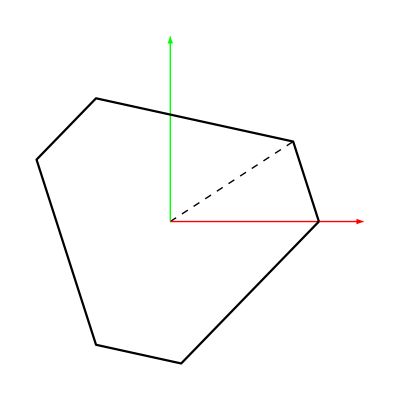

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

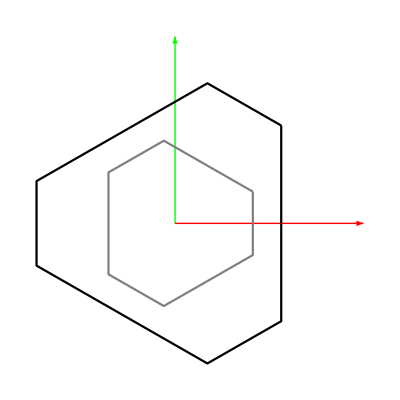

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{0.732576,0.680685,0},{0.223203,0.974772,0},{-0.955779,0.294087,0},{-0.955779,-0.294087,0},{0.223203,-0.974772,0},{0.732576,-0.680685,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→0.732576,a1y→0.680685,a1z→0,a2x→0.223203,a2y→0.974772,a2z→0,a3x→-0.955779,a3y→0.294087,a3z→0,a4x→-0.955779,a4y→-0.294087,a4z→0,a5x→0.223203,a5y→-0.974772,a5z→0,a6x→0.732576,a6y→-0.680685,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
rootsC = ({{x->1.8700438348728161, y->-0.5235870043873335, z->0.-0.926898973258719 ⅈ, c1->0.-0.10569096861540776 ⅈ, c2->0.+0.7154784037290103 ⅈ, c3->0}, {x->1.8700438348728161, y->-0.5235870043873335, z->0.+0.926898973258719 ⅈ, c1->0.+0.10569096861540776 ⅈ, c2->0.-0.7154784037290103 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.-0.9685245785328371 ⅈ, c1->0.-0.6638886705593215 ⅈ, c2->0.-0.3422565386596551 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.+0.9685245785328371 ⅈ, c1->0.+0.6638886705593215 ⅈ, c2->0.+0.3422565386596551 ⅈ, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.-1.3894731322781502 ⅈ, c1->0.+0.6338547336758182 ⅈ, c2->0.-0.42758251604766423 ⅈ, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.+1.3894731322781502 ⅈ, c1->0.-0.6338547336758182 ⅈ, c2->0.+0.42758251604766423 ⅈ, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
initposeC = Join[qx/.roots[[1]],iksolC[qx/.rootsC[[1]]]][[;;-7]];
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→0.628916,yt1→-0.430149,zt1→0.91962},{xt2→0.449784,yt2→-0.557918,zt2→0.245515},{xt3→0.127107,yt3→-0.844307,zt3→0.153522},{xt4→-0.212447,yt4→-1.17689,zt4→0.679753},{xt5→-0.101009,yt5→-1.09741,zt5→1.09912},{xt6→0.417678,yt6→-0.637052,zt6→1.24699}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→0.732576,yb1→0.680685,zb1→0},{xb2→0.223203,yb2→0.974772,zb2→0},{xb3→-0.955779,yb3→0.294087,zb3→0},{xb4→-0.955779,yb4→-0.294087,zb4→0},{xb5→0.223203,yb5→-0.974772,zb5→0},{xb6→0.732576,yb6→-0.680685,zb6→0}}

```mathematica
roots[[1]]
```

{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→8/11,yb1→11/16,zb1→0},{xb2→2/9,yb2→28/29,zb2→0},{xb3→-19/20,yb3→2/7,zb3→0},{xb4→-19/20,yb4→-2/7,zb4→0},{xb5→2/9,yb5→-29/30,zb5→0},{xb6→8/11,yb6→-13/19,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Plotting the SRSPM:

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
```

```mathematica
qfull = Join[qx, qvar];
```

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
index = 2;
initpose = Join[qx/.roots[[index]], iksolC[qx/.roots[[index]]]];
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]]]
```

-Graphics3D-

```mathematica
(*To plot only the top platform*)
```

```mathematica
(*plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.8],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, axis]
]*)
```

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

```mathematica
scale = 0.2;
parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]};
(*parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0};*)
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

## Newton-Raphson method for root tracking

### Real roots:

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
legvals//MatrixForm
(*legvals//Im//Flatten//CForm*)
```

(1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
1.43774+0. ⅈ | 1.56187+0. ⅈ | 1.57869+0. ⅈ | 1.33818+0. ⅈ | 1.1625+0. ⅈ | 1.29637+0. ⅈ
1.43018+0. ⅈ | 1.55576+0. ⅈ | 1.57772+0. ⅈ | 1.33582+0. ⅈ | 1.17309+0. ⅈ | 1.30613+0. ⅈ
1.42325+0. ⅈ | 1.55043+0. ⅈ | 1.57578+0. ⅈ | 1.33234+0. ⅈ | 1.18407+0. ⅈ | 1.31598+0. ⅈ
1.41709+0. ⅈ | 1.54599+0. ⅈ | 1.57289+0. ⅈ | 1.32778+0. ⅈ | 1.19525+0. ⅈ | 1.32577+0. ⅈ
1.4118+0. ⅈ | 1.54251+0. ⅈ | 1.56909+0. ⅈ | 1.32221+0. ⅈ | 1.20646+0. ⅈ | 1.33536+0. ⅈ
1.40748+0. ⅈ | 1.54006+0. ⅈ | 1.56442+0. ⅈ | 1.31569+0. ⅈ | 1.21751+0. ⅈ | 1.34459+0. ⅈ
1.40419+0. ⅈ | 1.53868+0. ⅈ | 1.55897+0. ⅈ | 1.30833+0. ⅈ | 1.22825+0. ⅈ | 1.35333+0. ⅈ
1.40201+0. ⅈ | 1.53839+0. ⅈ | 1.5528+0. ⅈ | 1.30022+0. ⅈ | 1.23852+0. ⅈ | 1.36145+0. ⅈ
1.40097+0. ⅈ | 1.5392+0. ⅈ | 1.54601+0. ⅈ | 1.29148+0. ⅈ | 1.24816+0. ⅈ | 1.36883+0. ⅈ
1.40108+0. ⅈ | 1.54109+0. ⅈ | 1.53869+0. ⅈ | 1.28224+0. ⅈ | 1.25704+0. ⅈ | 1.37538+0. ⅈ
1.40235+0. ⅈ | 1.54403+0. ⅈ | 1.53096+0. ⅈ | 1.27262+0. ⅈ | 1.26504+0. ⅈ | 1.381+0. ⅈ
1.40476+0. ⅈ | 1.54797+0. ⅈ | 1.52293+0. ⅈ | 1.26278+0. ⅈ | 1.27204+0. ⅈ | 1.38561+0. ⅈ
1.40826+0. ⅈ | 1.55284+0. ⅈ | 1.51472+0. ⅈ | 1.25287+0. ⅈ | 1.27796+0. ⅈ | 1.38916+0. ⅈ
1.41278+0. ⅈ | 1.55855+0. ⅈ | 1.50646+0. ⅈ | 1.24304+0. ⅈ | 1.28272+0. ⅈ | 1.39159+0. ⅈ
1.41825+0. ⅈ | 1.56501+0. ⅈ | 1.49829+0. ⅈ | 1.23346+0. ⅈ | 1.28625+0. ⅈ | 1.39287+0. ⅈ
1.42457+0. ⅈ | 1.5721+0. ⅈ | 1.49033+0. ⅈ | 1.22427+0. ⅈ | 1.28852+0. ⅈ | 1.39298+0. ⅈ
1.43163+0. ⅈ | 1.57971+0. ⅈ | 1.48271+0. ⅈ | 1.21565+0. ⅈ | 1.28948+0. ⅈ | 1.39193+0. ⅈ
1.43931+0. ⅈ | 1.5877+0. ⅈ | 1.47555+0. ⅈ | 1.20773+0. ⅈ | 1.28914+0. ⅈ | 1.38973+0. ⅈ
1.44748+0. ⅈ | 1.59595+0. ⅈ | 1.46899+0. ⅈ | 1.20065+0. ⅈ | 1.28748+0. ⅈ | 1.3864+0. ⅈ
1.456+0. ⅈ | 1.60433+0. ⅈ | 1.46314+0. ⅈ | 1.19455+0. ⅈ | 1.28455+0. ⅈ | 1.382+0. ⅈ
1.46473+0. ⅈ | 1.6127+0. ⅈ | 1.45808+0. ⅈ | 1.18954+0. ⅈ | 1.28036+0. ⅈ | 1.37657+0. ⅈ
1.47354+0. ⅈ | 1.62092+0. ⅈ | 1.45392+0. ⅈ | 1.18571+0. ⅈ | 1.27498+0. ⅈ | 1.3702+0. ⅈ
1.48228+0. ⅈ | 1.62889+0. ⅈ | 1.45072+0. ⅈ | 1.18312+0. ⅈ | 1.26848+0. ⅈ | 1.36298+0. ⅈ
1.49081+0. ⅈ | 1.63646+0. ⅈ | 1.44854+0. ⅈ | 1.18184+0. ⅈ | 1.26094+0. ⅈ | 1.35499+0. ⅈ
1.49902+0. ⅈ | 1.64353+0. ⅈ | 1.44743+0. ⅈ | 1.18188+0. ⅈ | 1.25246+0. ⅈ | 1.34637+0. ⅈ
1.50677+0. ⅈ | 1.65+0. ⅈ | 1.44739+0. ⅈ | 1.18325+0. ⅈ | 1.24316+0. ⅈ | 1.33723+0. ⅈ
1.51395+0. ⅈ | 1.65577+0. ⅈ | 1.44844+0. ⅈ | 1.18591+0. ⅈ | 1.23318+0. ⅈ | 1.3277+0. ⅈ
1.52046+0. ⅈ | 1.66076+0. ⅈ | 1.45055+0. ⅈ | 1.18982+0. ⅈ | 1.22264+0. ⅈ | 1.31794+0. ⅈ
1.52621+0. ⅈ | 1.66489+0. ⅈ | 1.45369+0. ⅈ | 1.19491+0. ⅈ | 1.21171+0. ⅈ | 1.30809+0. ⅈ
1.5311+0. ⅈ | 1.66811+0. ⅈ | 1.45779+0. ⅈ | 1.20107+0. ⅈ | 1.20055+0. ⅈ | 1.2983+0. ⅈ
1.53508+0. ⅈ | 1.67038+0. ⅈ | 1.46279+0. ⅈ | 1.2082+0. ⅈ | 1.18934+0. ⅈ | 1.28874+0. ⅈ
1.53808+0. ⅈ | 1.67165+0. ⅈ | 1.46861+0. ⅈ | 1.21617+0. ⅈ | 1.17824+0. ⅈ | 1.27956+0. ⅈ
1.54007+0. ⅈ | 1.67192+0. ⅈ | 1.47513+0. ⅈ | 1.22483+0. ⅈ | 1.16745+0. ⅈ | 1.27092+0. ⅈ
1.54102+0. ⅈ | 1.67117+0. ⅈ | 1.48224+0. ⅈ | 1.23405+0. ⅈ | 1.15714+0. ⅈ | 1.26296+0. ⅈ
1.54092+0. ⅈ | 1.66943+0. ⅈ | 1.48984+0. ⅈ | 1.24365+0. ⅈ | 1.14748+0. ⅈ | 1.25582+0. ⅈ
1.53976+0. ⅈ | 1.66671+0. ⅈ | 1.49778+0. ⅈ | 1.25349+0. ⅈ | 1.13866+0. ⅈ | 1.24964+0. ⅈ
1.53756+0. ⅈ | 1.66305+0. ⅈ | 1.50595+0. ⅈ | 1.2634+0. ⅈ | 1.13083+0. ⅈ | 1.24452+0. ⅈ
1.53436+0. ⅈ | 1.6585+0. ⅈ | 1.5142+0. ⅈ | 1.27323+0. ⅈ | 1.12413+0. ⅈ | 1.24057+0. ⅈ
1.5302+0. ⅈ | 1.65314+0. ⅈ | 1.52242+0. ⅈ | 1.28283+0. ⅈ | 1.1187+0. ⅈ | 1.23784+0. ⅈ
1.52513+0. ⅈ | 1.64703+0. ⅈ | 1.53047+0. ⅈ | 1.29205+0. ⅈ | 1.11464+0. ⅈ | 1.2364+0. ⅈ
1.51923+0. ⅈ | 1.64026+0. ⅈ | 1.53822+0. ⅈ | 1.30075+0. ⅈ | 1.11202+0. ⅈ | 1.23627+0. ⅈ
1.51258+0. ⅈ | 1.63293+0. ⅈ | 1.54557+0. ⅈ | 1.30882+0. ⅈ | 1.1109+0. ⅈ | 1.23745+0. ⅈ
1.50527+0. ⅈ | 1.62516+0. ⅈ | 1.55239+0. ⅈ | 1.31613+0. ⅈ | 1.1113+0. ⅈ | 1.23992+0. ⅈ
1.49742+0. ⅈ | 1.61706+0. ⅈ | 1.5586+0. ⅈ | 1.32258+0. ⅈ | 1.11321+0. ⅈ | 1.24364+0. ⅈ
1.48914+0. ⅈ | 1.60875+0. ⅈ | 1.56411+0. ⅈ | 1.3281+0. ⅈ | 1.1166+0. ⅈ | 1.24853+0. ⅈ
1.48055+0. ⅈ | 1.60036+0. ⅈ | 1.56882+0. ⅈ | 1.33259+0. ⅈ | 1.1214+0. ⅈ | 1.25451+0. ⅈ
1.47178+0. ⅈ | 1.59203+0. ⅈ | 1.57268+0. ⅈ | 1.336+0. ⅈ | 1.12751+0. ⅈ | 1.26147+0. ⅈ
1.46298+0. ⅈ | 1.58388+0. ⅈ | 1.57563+0. ⅈ | 1.33829+0. ⅈ | 1.13483+0. ⅈ | 1.26927+0. ⅈ
1.45428+0. ⅈ | 1.57606+0. ⅈ | 1.57763+0. ⅈ | 1.33942+0. ⅈ | 1.1432+0. ⅈ | 1.27779+0. ⅈ
1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ)

```mathematica
(*legfunc = Interpolation[legvals]*)
```

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
Inner[List, q/.qrule, Table[_Complex, {i, Length[q]}], List]
```

{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Norm[nvec]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Print[loopcounter];
Return[tempphi];
]
```

```mathematica
initpose[[7;;]]
```

{0.00305624-8.47269×10^-17 ⅈ,-0.0668855-8.94098×10^-17 ⅈ,0.456963-1.88509×10^-16 ⅈ,0.546956-7.59383×10^-17 ⅈ,-0.0946901-9.49786×10^-17 ⅈ,0.00349011-7.94231×10^-17 ⅈ,0.336276-3.59163×10^-18 ⅈ,0.286891-1.94522×10^-16 ⅈ,-0.0210274-1.35667×10^-16 ⅈ,0.0247844-1.74422×10^-16 ⅈ,-0.395383-3.49377×10^-17 ⅈ,-0.379795-1.31157×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
testconfig = initpose[[7;;-7]];
```

```mathematica
tic[]
tempϕ = testconfig;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηconfig, cJηconfig];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

3

3

3

«47 more identical outputs»

Actual time consumed: 0.04176 seconds.

CPU time consumed: 0.041748 seconds.

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Inner[List, Join[qx, q/.qrule], Table[_Complex, {i, Length[Join[qx, q]]}], List]
```

{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
p
```

{p1,p2,p3,p4,p5,p6}

```mathematica
s
```

{s1,s2,s3,s4,s5,s6}

```mathematica
ηext//N
```

{0.732576-(0.220568 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)-(0.536747 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l1 Cos[ψ1] Sin[ϕ1],0.680685-(1.07349 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)-(0.220568 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l1 Sin[ψ1],-(1.07349 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)-(0.441137 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l1 Cos[ϕ1] Cos[ψ1],0.223203-(0.575121 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.0773559 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l2 Cos[ψ2] Sin[ϕ2],0.974772+(0.154712 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)-(0.575121 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l2 Sin[ψ2],(0.154712 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)-(1.15024 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l2 Cos[ϕ2] Cos[ψ2],-0.955779-(0.354553 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.459391 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l3 Cos[ψ3] Sin[ϕ3],0.294087+(0.918783 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)-(0.354553 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l3 Sin[ψ3],(0.918783 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)-(0.709105 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l3 Cos[ϕ3] Cos[ψ3],-0.955779+(0.354553 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.459391 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l4 Cos[ψ4] Sin[ϕ4],-0.294087+(0.918783 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)+(0.354553 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l4 Sin[ψ4],(0.918783 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)+(0.709105 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l4 Cos[ϕ4] Cos[ψ4],0.223203+(0.575121 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.0773559 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l5 Cos[ψ5] Sin[ϕ5],-0.974772+(0.154712 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)+(0.575121 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l5 Sin[ψ5],(0.154712 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)+(1.15024 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l5 Cos[ϕ5] Cos[ψ5],0.732576+(0.220568 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)-(0.536747 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l6 Cos[ψ6] Sin[ϕ6],-0.680685-(1.07349 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)+(0.220568 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l6 Sin[ψ6],-(1.07349 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)+(0.441137 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l6 Cos[ϕ6] Cos[ψ6]}

```mathematica
initpose
cηext@@initpose
```

{0.2,0,1.28,0.2,0,0,0.00305624-8.47269×10^-17 ⅈ,-0.0668855-8.94098×10^-17 ⅈ,0.456963-1.88509×10^-16 ⅈ,0.546956-7.59383×10^-17 ⅈ,-0.0946901-9.49786×10^-17 ⅈ,0.00349011-7.94231×10^-17 ⅈ,0.336276-3.59163×10^-18 ⅈ,0.286891-1.94522×10^-16 ⅈ,-0.0210274-1.35667×10^-16 ⅈ,0.0247844-1.74422×10^-16 ⅈ,-0.395383-3.49377×10^-17 ⅈ,-0.379795-1.31157×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

{-7.80626×10^-18-1.15633×10^-16 ⅈ,0.+4.902×10^-18 ⅈ,-2.22045×10^-16+2.06692×10^-18 ⅈ,2.77556×10^-17-1.39993×10^-16 ⅈ,-5.55112×10^-17+2.9267×10^-16 ⅈ,2.22045×10^-16+7.71624×10^-17 ⅈ,-1.11022×10^-16-2.68985×10^-16 ⅈ,3.46945×10^-17+2.14124×10^-16 ⅈ,-2.22045×10^-16+1.27234×10^-16 ⅈ,1.11022×10^-16-8.38346×10^-17 ⅈ,1.17961×10^-16+2.33547×10^-16 ⅈ,0.+5.78274×10^-17 ⅈ,-1.38778×10^-17-9.9097×10^-17 ⅈ,-2.22045×10^-16+3.71585×10^-17 ⅈ,-2.22045×10^-16-2.499×10^-17 ⅈ,1.75207×10^-16-9.51422×10^-17 ⅈ,-2.77556×10^-16+1.56756×10^-16 ⅈ,2.22045×10^-16-6.22413×10^-17 ⅈ}

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initpose[[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.03135 seconds.

CPU time consumed: 0.026526 seconds.

```mathematica
xlist = ϕlist[[;;, ;;3]];
```

```mathematica
xlist[[1]]
```

{0.2,0,1.28}

```mathematica
Graphics3D[Sphere[{Chop[xlist[[1;;]]]}, 0.01]]
```

-Graphics3D-

```mathematica
initposes = Table[Join[qx/.roots[[i]], iksolC[qx/.roots[[i]]]], {i, Length[roots]}];
```

```mathematica
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.02652 seconds.

CPU time consumed: 0.026504 seconds.

```mathematica
xlist = ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksolC[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

```mathematica
(*Tracking all the sets of roots together*)
```

```mathematica
testext = initposes[[;;, ;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = Table[NRTracking[legvals[[i]], tempϕ[[j]], cηext, cJηext],{j, Length[tempϕ]}];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.20656 seconds.

CPU time consumed: 0.206634 seconds.

```mathematica
ϕlist//Dimensions
```

{51,8,18}

```mathematica
ϕlist[[1]]//Dimensions
```

{8,18}

```mathematica
initpose
```

{0.2,0,1.28,0.2,0,0,0.00305624-8.47269×10^-17 ⅈ,-0.0668855-8.94098×10^-17 ⅈ,0.456963-1.88509×10^-16 ⅈ,0.546956-7.59383×10^-17 ⅈ,-0.0946901-9.49786×10^-17 ⅈ,0.00349011-7.94231×10^-17 ⅈ,0.336276-3.59163×10^-18 ⅈ,0.286891-1.94522×10^-16 ⅈ,-0.0210274-1.35667×10^-16 ⅈ,0.0247844-1.74422×10^-16 ⅈ,-0.395383-3.49377×10^-17 ⅈ,-0.379795-1.31157×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
tempU = 51;
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[tempU]], iksolC[xlist[[tempU]]]], List]],ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-1.436630585725502,-2.436545269611847,1.857239809311155},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.029245185453707287,-0.04235819972678877,0.9986743723775453}]
```

-Graphics3D-

### Complex roots:

```mathematica
(* Now tracking the other roots *)
```

```mathematica
initposesC = Table[Join[qx/.rootsC[[i]], iksolC[qx/.rootsC[[i]]]], {i, Length[rootsC]}];
```

```mathematica
initposesC[[1]][[;;-7]]//CForm;
```

```mathematica
(*LinearSolve overflow occured in computation*)
```

```mathematica
initposesC//MatrixForm
```

(1.87004 | -0.523587 | 0.-0.926899 ⅈ | 0.-0.105691 ⅈ | 0.+0.715478 ⅈ | 0 | 1.5708+1.5263 ⅈ | 1.5708+0.691399 ⅈ | 1.5708-0.199792 ⅈ | 1.5708-0.523049 ⅈ | 1.5708+0.377184 ⅈ | 1.5708+1.39851 ⅈ | 0.58897+4.89195×10^-18 ⅈ | 0.627358-9.45687×10^-17 ⅈ | 0.384532-1.24753×10^-17 ⅈ | 0.591043-6.21292×10^-17 ⅈ | 0.152795-1.09198×10^-16 ⅈ | -0.0749872+3.34157×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
1.87004 | -0.523587 | 0.+0.926899 ⅈ | 0.+0.105691 ⅈ | 0.-0.715478 ⅈ | 0 | 1.5708-1.5263 ⅈ | 1.5708-0.691399 ⅈ | 1.5708+0.199792 ⅈ | 1.5708+0.523049 ⅈ | 1.5708-0.377184 ⅈ | 1.5708-1.39851 ⅈ | 0.58897+4.89195×10^-18 ⅈ | 0.627358-9.45687×10^-17 ⅈ | 0.384532-1.24753×10^-17 ⅈ | 0.591043-6.21292×10^-17 ⅈ | 0.152795-1.09198×10^-16 ⅈ | -0.0749872+3.34157×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-1.07203 | 1.69713 | 0.-0.968525 ⅈ | 0.-0.663889 ⅈ | 0.-0.342257 ⅈ | 0 | -1.5708-0.79459 ⅈ | 3.14159-0.891289 ⅈ | -3.14159-0.461391 ⅈ | -3.14159-0.948897 ⅈ | -1.5708+1.03751 ⅈ | -1.5708+0.855051 ⅈ | -0.891722-1.77951×10^-16 ⅈ | -1.5708+1.05398 ⅈ | -1.5708+1.23224 ⅈ | -1.5708+0.304463 ⅈ | -1.10481-1.2291×10^-16 ⅈ | -1.13345-8.52749×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-1.07203 | 1.69713 | 0.+0.968525 ⅈ | 0.+0.663889 ⅈ | 0.+0.342257 ⅈ | 0 | -1.5708+0.79459 ⅈ | 0.+0.891289 ⅈ | 9.7762×10^-33+0.461391 ⅈ | 0.+0.948897 ⅈ | -1.5708-1.03751 ⅈ | -1.5708-0.855051 ⅈ | -0.891722-1.77951×10^-16 ⅈ | -1.5708+1.05398 ⅈ | -1.5708+1.23224 ⅈ | -1.5708+0.304463 ⅈ | -1.10481-1.2291×10^-16 ⅈ | -1.13345-8.52749×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.218338 | -0.790621 | 0.724086 | -0.715499 | -0.645258 | 0 | -0.112247+8.56472×10^-18 ⅈ | 0.745313-7.71044×10^-17 ⅈ | 1.42996-1.01235×10^-16 ⅈ | 0.830045-9.02313×10^-17 ⅈ | -0.28684-1.57524×10^-16 ⅈ | -0.247355+3.26621×10^-18 ⅈ | 0.876191-1.51332×10^-16 ⅈ | 1.35618+8.56498×10^-18 ⅈ | 0.805412-9.38911×10^-18 ⅈ | 0.719639-1.94225×10^-16 ⅈ | 0.106613-2.04007×10^-17 ⅈ | -0.0339125-1.00511×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.2 | 0 | 1.28 | 0.2 | 0 | 0 | 0.00305624-8.47269×10^-17 ⅈ | -0.0668855-8.94098×10^-17 ⅈ | 0.456963-1.88509×10^-16 ⅈ | 0.546956-7.59383×10^-17 ⅈ | -0.0946901-9.49786×10^-17 ⅈ | 0.00349011-7.94231×10^-17 ⅈ | 0.336276-3.59163×10^-18 ⅈ | 0.286891-1.94522×10^-16 ⅈ | -0.0210274-1.35667×10^-16 ⅈ | 0.0247844-1.74422×10^-16 ⅈ | -0.395383-3.49377×10^-17 ⅈ | -0.379795-1.31157×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.513695 | -0.519996 | -0.798723 | -0.333759 | -0.951699 | 0 | -1.88547-1.05103×10^-16 ⅈ | -2.65366+2.74726×10^-17 ⅈ | 2.78228+1.86009×10^-17 ⅈ | 2.89251-1.51877×10^-16 ⅈ | -2.20522+5.34046×10^-17 ⅈ | -1.74294-1.42102×10^-16 ⅈ | 0.61606-1.17742×10^-16 ⅈ | 0.697469-2.13889×10^-16 ⅈ | 0.419763+1.94314×10^-17 ⅈ | 0.5377-1.52741×10^-16 ⅈ | 0.0705025-6.62747×10^-17 ⅈ | -0.103948+3.0597×10^-18 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.524434 | 0.268509 | 1.0308 | 0.603749 | -0.188561 | 0 | 0.192004-1.13031×10^-16 ⅈ | 0.0889258-1.7415×10^-16 ⅈ | 0.682842-1.62916×10^-16 ⅈ | 1.07125+2.17808×10^-17 ⅈ | 0.558764-4.21848×10^-17 ⅈ | 0.329797-6.88655×10^-17 ⅈ | 0.275819+9.64012×10^-18 ⅈ | 0.269746+5.15196×10^-17 ⅈ | -0.139217-2.71196×10^-17 ⅈ | -0.356444-2.07901×10^-16 ⅈ | -1.01698-1.89033×10^-16 ⅈ | -0.62811-1.10812×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.73374 | -2.15448 | 0.-1.38947 ⅈ | 0.+0.633855 ⅈ | 0.-0.427583 ⅈ | 0 | 0.+0.466788 ⅈ | -1.5708+0.672366 ⅈ | -3.14159-0.143883 ⅈ | 3.14159-0.335195 ⅈ | 3.14159-0.634022 ⅈ | 3.14159-1.03998 ⅈ | 1.5708-0.239649 ⅈ | 1.38808-1.65894×10^-16 ⅈ | 1.5708-0.72145 ⅈ | 1.5708-1.61497 ⅈ | 1.5708-1.59919 ⅈ | 1.5708-0.452074 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.73374 | -2.15448 | 0.+1.38947 ⅈ | 0.-0.633855 ⅈ | 0.+0.427583 ⅈ | 0 | -3.14159-0.466788 ⅈ | -1.5708-0.672366 ⅈ | 1.42334×10^-32+0.143883 ⅈ | 8.61715×10^-33+0.335195 ⅈ | -1.16183×10^-32+0.634022 ⅈ | 1.74361×10^-32+1.03998 ⅈ | 1.5708-0.239649 ⅈ | 1.38808-1.65894×10^-16 ⅈ | 1.5708-0.72145 ⅈ | 1.5708-1.61497 ⅈ | 1.5708-1.59919 ⅈ | 1.5708-0.452074 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.2 | 0 | -1.28 | -0.2 | 0 | 0 | 3.13854-8.47269×10^-17 ⅈ | -3.07471-8.94098×10^-17 ⅈ | 2.68463-1.88509×10^-16 ⅈ | 2.59464-7.59383×10^-17 ⅈ | -3.0469-9.49786×10^-17 ⅈ | 3.1381-7.94231×10^-17 ⅈ | 0.336276-3.59163×10^-18 ⅈ | 0.286891-1.94522×10^-16 ⅈ | -0.0210274-1.35667×10^-16 ⅈ | 0.0247844-1.74422×10^-16 ⅈ | -0.395383-3.49377×10^-17 ⅈ | -0.379795-1.31157×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.513695 | -0.519996 | 0.798723 | 0.333759 | 0.951699 | 0 | -1.25612-1.05103×10^-16 ⅈ | -0.487928+7.95195×10^-17 ⅈ | 0.359309+1.86009×10^-17 ⅈ | 0.249078-1.51877×10^-16 ⅈ | -0.93637+5.34046×10^-17 ⅈ | -1.39865-1.42102×10^-16 ⅈ | 0.61606-1.17742×10^-16 ⅈ | 0.697469-2.13889×10^-16 ⅈ | 0.419763+1.94314×10^-17 ⅈ | 0.5377-1.52741×10^-16 ⅈ | 0.0705025-6.62747×10^-17 ⅈ | -0.103948+3.0597×10^-18 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.218338 | -0.790621 | -0.724086 | 0.715499 | 0.645258 | 0 | -3.02935+1.16737×10^-17 ⅈ | 2.39628-7.71044×10^-17 ⅈ | 1.71163-1.01235×10^-16 ⅈ | 2.31155-9.02313×10^-17 ⅈ | -2.85475-1.57524×10^-16 ⅈ | -2.89424+3.26621×10^-18 ⅈ | 0.876191-1.51332×10^-16 ⅈ | 1.35618+8.56498×10^-18 ⅈ | 0.805412-9.38911×10^-18 ⅈ | 0.719639-1.94225×10^-16 ⅈ | 0.106613-2.04007×10^-17 ⅈ | -0.0339125-1.00511×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.524434 | 0.268509 | -1.0308 | -0.603749 | 0.188561 | 0 | 2.94959-1.13031×10^-16 ⅈ | 3.05267-1.7415×10^-16 ⅈ | 2.45875-1.62916×10^-16 ⅈ | 2.07034-3.14016×10^-17 ⅈ | 2.58283-4.21848×10^-17 ⅈ | 2.8118-6.88655×10^-17 ⅈ | 0.275819+9.64012×10^-18 ⅈ | 0.269746+5.15196×10^-17 ⅈ | -0.139217-2.71196×10^-17 ⅈ | -0.356444-2.07901×10^-16 ⅈ | -1.01698-1.89033×10^-16 ⅈ | -0.62811-1.10812×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ)

```mathematica
initposesC[[1]][[;;-7]]//CForm
```

List(1.8700438348728161,-0.5235870043873335,Complex(0.,-0.926898973258719),Complex(0.,-0.10569096861540776),Complex(0.,0.7154784037290103),0,
   Complex(1.5707963267948966,1.526295957741447),Complex(1.5707963267948966,0.6913993396133373),Complex(1.5707963267948966,-0.1997919002830573),
   Complex(1.5707963267948966,-0.5230490884925065),Complex(1.5707963267948966,0.37718441615032144),Complex(1.5707963267948966,1.3985097660833),
   Complex(0.5889695511742917,4.8919532403342845e-18),Complex(0.6273584382908439,-9.456869853007833e-17),Complex(0.38453167003247346,-1.2475304943139138e-17),
   Complex(0.5910427650086758,-6.21291993862106e-17),Complex(0.15279452223188406,-1.091982750937909e-16),Complex(-0.07498723590723586,3.3415727902921217e-17))

```mathematica
(*Tracking a complex root*)
```

```mathematica
testext = initposesC[[1]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ,cηext,cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

3

3

3

«47 more identical outputs»

Actual time consumed: 0.01451 seconds.

CPU time consumed: 0.0145 seconds.

```mathematica
(*Tracking all the sets of roots (Real + Complex) together*)
```

```mathematica
testext = initposesC[[;;, ;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤5, i++, 
tempϕ = Table[NRTracking[legvals[[i]], tempϕ[[j]], cηext, cJηext],{j, Length[tempϕ]}];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

3

3

3

«53 more identical outputs»

Actual time consumed: 0.01624 seconds.

CPU time consumed: 0.016242 seconds.

```mathematica
ϕlist//MatrixForm
```

((1.87004
-0.523587
0.-0.926899 ⅈ
0.-0.105691 ⅈ
0.+0.715478 ⅈ
0
1.5708+1.5263 ⅈ
1.5708+0.691399 ⅈ
1.5708-0.199792 ⅈ
1.5708-0.523049 ⅈ
1.5708+0.377184 ⅈ
1.5708+1.39851 ⅈ
0.58897+4.89195×10^-18 ⅈ
0.627358-9.45687×10^-17 ⅈ
0.384532-1.24753×10^-17 ⅈ
0.591043-6.21292×10^-17 ⅈ
0.152795-1.09198×10^-16 ⅈ
-0.0749872+3.34157×10^-17 ⅈ) | (1.87004
-0.523587
0.+0.926899 ⅈ
0.+0.105691 ⅈ
0.-0.715478 ⅈ
0
1.5708-1.5263 ⅈ
1.5708-0.691399 ⅈ
1.5708+0.199792 ⅈ
1.5708+0.523049 ⅈ
1.5708-0.377184 ⅈ
1.5708-1.39851 ⅈ
0.58897+4.89195×10^-18 ⅈ
0.627358-9.45687×10^-17 ⅈ
0.384532-1.24753×10^-17 ⅈ
0.591043-6.21292×10^-17 ⅈ
0.152795-1.09198×10^-16 ⅈ
-0.0749872+3.34157×10^-17 ⅈ) | (-1.07203
1.69713
0.-0.968525 ⅈ
0.-0.663889 ⅈ
0.-0.342257 ⅈ
0
-1.5708-0.79459 ⅈ
3.14159-0.891289 ⅈ
-3.14159-0.461391 ⅈ
-3.14159-0.948897 ⅈ
-1.5708+1.03751 ⅈ
-1.5708+0.855051 ⅈ
-0.891722-1.77951×10^-16 ⅈ
-1.5708+1.05398 ⅈ
-1.5708+1.23224 ⅈ
-1.5708+0.304463 ⅈ
-1.10481-1.2291×10^-16 ⅈ
-1.13345-8.52749×10^-17 ⅈ) | (-1.07203
1.69713
0.+0.968525 ⅈ
0.+0.663889 ⅈ
0.+0.342257 ⅈ
0
-1.5708+0.79459 ⅈ
0.+0.891289 ⅈ
9.7762×10^-33+0.461391 ⅈ
0.+0.948897 ⅈ
-1.5708-1.03751 ⅈ
-1.5708-0.855051 ⅈ
-0.891722-1.77951×10^-16 ⅈ
-1.5708+1.05398 ⅈ
-1.5708+1.23224 ⅈ
-1.5708+0.304463 ⅈ
-1.10481-1.2291×10^-16 ⅈ
-1.13345-8.52749×10^-17 ⅈ) | (0.218338
-0.790621
0.724086
-0.715499
-0.645258
0
-0.112247+8.56472×10^-18 ⅈ
0.745313-7.71044×10^-17 ⅈ
1.42996-1.01235×10^-16 ⅈ
0.830045-9.02313×10^-17 ⅈ
-0.28684-1.57524×10^-16 ⅈ
-0.247355+3.26621×10^-18 ⅈ
0.876191-1.51332×10^-16 ⅈ
1.35618+8.56498×10^-18 ⅈ
0.805412-9.38911×10^-18 ⅈ
0.719639-1.94225×10^-16 ⅈ
0.106613-2.04007×10^-17 ⅈ
-0.0339125-1.00511×10^-16 ⅈ) | (0.2
0
1.28
0.2
0
0
0.00305624-8.47269×10^-17 ⅈ
-0.0668855-8.94098×10^-17 ⅈ
0.456963-1.88509×10^-16 ⅈ
0.546956-7.59383×10^-17 ⅈ
-0.0946901-9.49786×10^-17 ⅈ
0.00349011-7.94231×10^-17 ⅈ
0.336276-3.59163×10^-18 ⅈ
0.286891-1.94522×10^-16 ⅈ
-0.0210274-1.35667×10^-16 ⅈ
0.0247844-1.74422×10^-16 ⅈ
-0.395383-3.49377×10^-17 ⅈ
-0.379795-1.31157×10^-16 ⅈ) | (-0.513695
-0.519996
-0.798723
-0.333759
-0.951699
0
-1.88547-1.05103×10^-16 ⅈ
-2.65366+2.74726×10^-17 ⅈ
2.78228+1.86009×10^-17 ⅈ
2.89251-1.51877×10^-16 ⅈ
-2.20522+5.34046×10^-17 ⅈ
-1.74294-1.42102×10^-16 ⅈ
0.61606-1.17742×10^-16 ⅈ
0.697469-2.13889×10^-16 ⅈ
0.419763+1.94314×10^-17 ⅈ
0.5377-1.52741×10^-16 ⅈ
0.0705025-6.62747×10^-17 ⅈ
-0.103948+3.0597×10^-18 ⅈ) | (0.524434
0.268509
1.0308
0.603749
-0.188561
0
0.192004-1.13031×10^-16 ⅈ
0.0889258-1.7415×10^-16 ⅈ
0.682842-1.62916×10^-16 ⅈ
1.07125+2.17808×10^-17 ⅈ
0.558764-4.21848×10^-17 ⅈ
0.329797-6.88655×10^-17 ⅈ
0.275819+9.64012×10^-18 ⅈ
0.269746+5.15196×10^-17 ⅈ
-0.139217-2.71196×10^-17 ⅈ
-0.356444-2.07901×10^-16 ⅈ
-1.01698-1.89033×10^-16 ⅈ
-0.62811-1.10812×10^-16 ⅈ) | (-0.73374
-2.15448
0.-1.38947 ⅈ
0.+0.633855 ⅈ
0.-0.427583 ⅈ
0
0.+0.466788 ⅈ
-1.5708+0.672366 ⅈ
-3.14159-0.143883 ⅈ
3.14159-0.335195 ⅈ
3.14159-0.634022 ⅈ
3.14159-1.03998 ⅈ
1.5708-0.239649 ⅈ
1.38808-1.65894×10^-16 ⅈ
1.5708-0.72145 ⅈ
1.5708-1.61497 ⅈ
1.5708-1.59919 ⅈ
1.5708-0.452074 ⅈ) | (-0.73374
-2.15448
0.+1.38947 ⅈ
0.-0.633855 ⅈ
0.+0.427583 ⅈ
0
-3.14159-0.466788 ⅈ
-1.5708-0.672366 ⅈ
1.42334×10^-32+0.143883 ⅈ
8.61715×10^-33+0.335195 ⅈ
-1.16183×10^-32+0.634022 ⅈ
1.74361×10^-32+1.03998 ⅈ
1.5708-0.239649 ⅈ
1.38808-1.65894×10^-16 ⅈ
1.5708-0.72145 ⅈ
1.5708-1.61497 ⅈ
1.5708-1.59919 ⅈ
1.5708-0.452074 ⅈ) | (0.2
0
-1.28
-0.2
0
0
3.13854-8.47269×10^-17 ⅈ
-3.07471-8.94098×10^-17 ⅈ
2.68463-1.88509×10^-16 ⅈ
2.59464-7.59383×10^-17 ⅈ
-3.0469-9.49786×10^-17 ⅈ
3.1381-7.94231×10^-17 ⅈ
0.336276-3.59163×10^-18 ⅈ
0.286891-1.94522×10^-16 ⅈ
-0.0210274-1.35667×10^-16 ⅈ
0.0247844-1.74422×10^-16 ⅈ
-0.395383-3.49377×10^-17 ⅈ
-0.379795-1.31157×10^-16 ⅈ) | (-0.513695
-0.519996
0.798723
0.333759
0.951699
0
-1.25612-1.05103×10^-16 ⅈ
-0.487928+7.95195×10^-17 ⅈ
0.359309+1.86009×10^-17 ⅈ
0.249078-1.51877×10^-16 ⅈ
-0.93637+5.34046×10^-17 ⅈ
-1.39865-1.42102×10^-16 ⅈ
0.61606-1.17742×10^-16 ⅈ
0.697469-2.13889×10^-16 ⅈ
0.419763+1.94314×10^-17 ⅈ
0.5377-1.52741×10^-16 ⅈ
0.0705025-6.62747×10^-17 ⅈ
-0.103948+3.0597×10^-18 ⅈ) | (0.218338
-0.790621
-0.724086
0.715499
0.645258
0
-3.02935+1.16737×10^-17 ⅈ
2.39628-7.71044×10^-17 ⅈ
1.71163-1.01235×10^-16 ⅈ
2.31155-9.02313×10^-17 ⅈ
-2.85475-1.57524×10^-16 ⅈ
-2.89424+3.26621×10^-18 ⅈ
0.876191-1.51332×10^-16 ⅈ
1.35618+8.56498×10^-18 ⅈ
0.805412-9.38911×10^-18 ⅈ
0.719639-1.94225×10^-16 ⅈ
0.106613-2.04007×10^-17 ⅈ
-0.0339125-1.00511×10^-16 ⅈ) | (0.524434
0.268509
-1.0308
-0.603749
0.188561
0
2.94959-1.13031×10^-16 ⅈ
3.05267-1.7415×10^-16 ⅈ
2.45875-1.62916×10^-16 ⅈ
2.07034-3.14016×10^-17 ⅈ
2.58283-4.21848×10^-17 ⅈ
2.8118-6.88655×10^-17 ⅈ
0.275819+9.64012×10^-18 ⅈ
0.269746+5.15196×10^-17 ⅈ
-0.139217-2.71196×10^-17 ⅈ
-0.356444-2.07901×10^-16 ⅈ
-1.01698-1.89033×10^-16 ⅈ
-0.62811-1.10812×10^-16 ⅈ)
(1.89273+1.31872×10^-24 ⅈ
-0.496254+2.40463×10^-24 ⅈ
2.71267×10^-24-0.949611 ⅈ
-8.34689×10^-25-0.104205 ⅈ
-1.97001×10^-25+0.717854 ⅈ
2.24741×10^-16-4.7814×10^-25 ⅈ
1.5708+1.53353 ⅈ
1.5708+0.697911 ⅈ
1.5708-0.193068 ⅈ
1.5708-0.507732 ⅈ
1.5708+0.390848 ⅈ
1.5708+1.4077 ⅈ
0.570773+9.10336×10^-26 ⅈ
0.609393-1.81808×10^-24 ⅈ
0.36573-2.82467×10^-24 ⅈ
0.566361-4.14236×10^-24 ⅈ
0.127127-2.74058×10^-24 ⅈ
-0.0951996-1.61798×10^-25 ⅈ) | (1.89273-1.31905×10^-24 ⅈ
-0.496254-2.40477×10^-24 ⅈ
2.71296×10^-24+0.949611 ⅈ
-8.34764×10^-25+0.104205 ⅈ
-1.97148×10^-25-0.717854 ⅈ
4.20897×10^-16+4.7817×10^-25 ⅈ
1.5708-1.53353 ⅈ
1.5708-0.697911 ⅈ
1.5708+0.193068 ⅈ
1.5708+0.507732 ⅈ
1.5708-0.390848 ⅈ
1.5708-1.4077 ⅈ
0.570773-9.0867×10^-26 ⅈ
0.609393+1.81823×10^-24 ⅈ
0.36573+2.82478×10^-24 ⅈ
0.566361+4.1426×10^-24 ⅈ
0.127127+2.74075×10^-24 ⅈ
-0.0951996+1.61937×10^-25 ⅈ) | (-1.05554-1.74425×10^-23 ⅈ
1.69321-1.22981×10^-23 ⅈ
-1.95476×10^-24-0.955035 ⅈ
3.0977×10^-24-0.661635 ⅈ
-5.42059×10^-24-0.340667 ⅈ
9.70876×10^-17-4.69473×10^-24 ⅈ
-1.5708-0.794094 ⅈ
3.14159-0.890413 ⅈ
-3.14159-0.456226 ⅈ
-3.14159-0.922548 ⅈ
-1.5708+1.03475 ⅈ
-1.5708+0.852344 ⅈ
-0.897079+1.51058×10^-23 ⅈ
-1.5708+1.0476 ⅈ
-1.5708+1.2228 ⅈ
-1.5708+0.305618 ⅈ
-1.1124+4.48421×10^-23 ⅈ
-1.14055+4.15015×10^-23 ⅈ) | (-1.05554+2.91392×10^-24 ⅈ
1.69321-4.81058×10^-24 ⅈ
5.8274×10^-24+0.955035 ⅈ
6.34753×10^-25+0.661635 ⅈ
7.35234×10^-25+0.340667 ⅈ
-8.78457×10^-17-1.30275×10^-25 ⅈ
-1.5708+0.794094 ⅈ
-5.35844×10^-25+0.890413 ⅈ
1.42118×10^-24+0.456226 ⅈ
-2.33119×10^-23+0.922548 ⅈ
-1.5708-1.03475 ⅈ
-1.5708-0.852344 ⅈ
-0.897079+4.38429×10^-24 ⅈ
-1.5708+1.0476 ⅈ
-1.5708+1.2228 ⅈ
-1.5708+0.305618 ⅈ
-1.1124-6.13533×10^-25 ⅈ
-1.14055-6.10347×10^-25 ⅈ) | (0.226376-1.52095×10^-28 ⅈ
-0.77354-7.40545×10^-29 ⅈ
0.735889-1.06081×10^-28 ⅈ
-0.72687-1.54085×10^-29 ⅈ
-0.64838-7.6556×10^-29 ⅈ
-4.06619×10^-15+1.44968×10^-29 ⅈ
-0.101265-4.76728×10^-28 ⅈ
0.74887+1.8791×10^-27 ⅈ
1.42027+9.06479×10^-29 ⅈ
0.82332-4.28778×10^-29 ⅈ
-0.279011-1.49392×10^-28 ⅈ
-0.239973-1.6391×10^-28 ⅈ
0.864339+3.47448×10^-30 ⅈ
1.34567+3.66272×10^-28 ⅈ
0.795508+1.55832×10^-28 ⅈ
0.701834+1.59101×10^-28 ⅈ
0.0856551+5.1485×10^-29 ⅈ
-0.0507742+7.64773×10^-30 ⅈ) | (0.198423-9.47229×10^-31 ⅈ
0.0250666+1.70996×10^-30 ⅈ
1.28-2.82433×10^-30 ⅈ
0.2+8.20517×10^-30 ⅈ
8.44136×10^-17+1.13515×10^-30 ⅈ
6.9874×10^-17-3.09006×10^-30 ⅈ
0.00190076-1.90706×10^-30 ⅈ
-0.0679313+1.94708×10^-30 ⅈ
0.456066+1.9472×10^-30 ⅈ
0.54595+1.57869×10^-30 ⅈ
-0.096166-3.07301×10^-30 ⅈ
0.00217059-1.70802×10^-30 ⅈ
0.319818+3.87235×10^-30 ⅈ
0.271478+1.55339×10^-30 ⅈ
-0.0369119-2.05903×10^-30 ⅈ
0.00607235-7.09202×10^-30 ⅈ
-0.415234-7.84116×10^-30 ⅈ
-0.397756+6.51184×10^-31 ⅈ) | (-0.517278+1.16644×10^-27 ⅈ
-0.492665+4.68628×10^-28 ⅈ
-0.813533+2.4261×10^-27 ⅈ
-0.332096-7.93659×10^-28 ⅈ
-0.952486-4.92512×10^-28 ⅈ
3.78515×10^-15-1.05968×10^-27 ⅈ
-1.89557+1.98418×10^-27 ⅈ
-2.65591-9.57998×10^-29 ⅈ
2.78802-1.9003×10^-27 ⅈ
2.89791-1.097×10^-27 ⅈ
-2.21484+4.11485×10^-28 ⅈ
-1.7538+1.00834×10^-27 ⅈ
0.597289+6.16248×10^-28 ⅈ
0.677825+1.54247×10^-27 ⅈ
0.400169+6.707×10^-28 ⅈ
0.514416+8.57841×10^-29 ⅈ
0.0468065-1.02965×10^-27 ⅈ
-0.123639-8.49999×10^-28 ⅈ) | (0.516913+6.46615×10^-30 ⅈ
0.286635-8.08097×10^-29 ⅈ
1.03254+7.60029×10^-30 ⅈ
0.59631-7.31965×10^-29 ⅈ
-0.184595+4.13979×10^-29 ⅈ
-5.14152×10^-16+3.82998×10^-29 ⅈ
0.188171+8.74964×10^-30 ⅈ
0.0854979+5.07441×10^-31 ⅈ
0.678667-1.4839×10^-30 ⅈ
1.06402-2.49758×10^-29 ⅈ
0.540723-1.65377×10^-28 ⅈ
0.322746+2.04071×10^-31 ⅈ
0.261279+4.7197×10^-30 ⅈ
0.255734+2.73043×10^-29 ⅈ
-0.151612+6.10796×10^-29 ⅈ
-0.367184+1.18177×10^-28 ⅈ
-1.02377+1.05687×10^-28 ⅈ
-0.640393+3.74976×10^-29 ⅈ) | (-0.758962+4.52959×10^-24 ⅈ
-2.16662-4.21009×10^-24 ⅈ
1.2381×10^-24-1.41146 ⅈ
6.82099×10^-25+0.637004 ⅈ
2.04513×10^-24-0.428145 ⅈ
-6.7411×10^-16-2.19825×10^-24 ⅈ
-5.39696×10^-24+0.508116 ⅈ
-1.5708+0.657046 ⅈ
-3.14159-0.160317 ⅈ
3.14159-0.342386 ⅈ
3.14159-0.63838 ⅈ
3.14159-1.06336 ⅈ
1.5708-0.237946 ⅈ
1.37859+1.3377×10^-23 ⅈ
1.5708-0.727922 ⅈ
1.5708-1.62728 ⅈ
1.5708-1.60332 ⅈ
1.5708-0.449621 ⅈ) | (-0.758962-1.84719×10^-24 ⅈ
-2.16662+2.08102×10^-25 ⅈ
-1.1206×10^-24+1.41146 ⅈ
2.44704×10^-25-0.637004 ⅈ
4.26328×10^-25+0.428145 ⅈ
-1.79415×10^-16+1.58982×10^-25 ⅈ
-3.14159-0.508116 ⅈ
-1.5708-0.657046 ⅈ
4.48119×10^-25+0.160317 ⅈ
3.16158×10^-25+0.342386 ⅈ
-3.47687×10^-25+0.63838 ⅈ
-1.72805×10^-23+1.06336 ⅈ
1.5708-0.237946 ⅈ
1.37859-3.17456×10^-24 ⅈ
1.5708-0.727922 ⅈ
1.5708-1.62728 ⅈ
1.5708-1.60332 ⅈ
1.5708-0.449621 ⅈ) | (0.198423+7.75608×10^-33 ⅈ
0.0250666+1.10869×10^-30 ⅈ
-1.28+2.82109×10^-30 ⅈ
-0.2-8.37701×10^-30 ⅈ
-1.38762×10^-16-1.05088×10^-30 ⅈ
-3.0207×10^-17-2.86499×10^-30 ⅈ
3.13969+1.38531×10^-30 ⅈ
-3.07366-2.36205×10^-30 ⅈ
2.68553-2.4384×10^-30 ⅈ
2.59564-2.43489×10^-30 ⅈ
-3.04543+1.71814×10^-30 ⅈ
3.13942+8.24902×10^-31 ⅈ
0.319818+4.2111×10^-30 ⅈ
0.271478+1.99173×10^-30 ⅈ
-0.0369119-1.58382×10^-30 ⅈ
0.00607235-6.5663×10^-30 ⅈ
-0.415234-7.42653×10^-30 ⅈ
-0.397756+9.898×10^-31 ⅈ) | (-0.517278+8.03671×10^-28 ⅈ
-0.492665-2.39895×10^-28 ⅈ
0.813533-2.09739×10^-27 ⅈ
0.332096+1.27454×10^-27 ⅈ
0.952486+1.14363×10^-27 ⅈ
3.87696×10^-15-1.02279×10^-27 ⅈ
-1.24602-1.26868×10^-27 ⅈ
-0.485683+2.5821×10^-28 ⅈ
0.353576+1.67091×10^-27 ⅈ
0.243682+7.44691×10^-28 ⅈ
-0.926757-6.70528×10^-28 ⅈ
-1.3878-9.17974×10^-28 ⅈ
0.597289+7.22871×10^-28 ⅈ
0.677825+1.69586×10^-27 ⅈ
0.400169+1.12471×10^-27 ⅈ
0.514416+6.74459×10^-28 ⅈ
0.0468065-3.69205×10^-28 ⅈ
-0.123639-4.19088×10^-28 ⅈ) | (0.226376-5.92967×10^-29 ⅈ
-0.77354+7.61075×10^-29 ⅈ
-0.735889+2.37474×10^-28 ⅈ
0.72687+9.01534×10^-29 ⅈ
0.64838+1.16805×10^-28 ⅈ
-3.4604×10^-15+1.1835×10^-28 ⅈ
-3.04033+2.04808×10^-28 ⅈ
2.39272-2.53289×10^-28 ⅈ
1.72132-2.11425×10^-28 ⅈ
2.31827-1.19645×10^-28 ⅈ
-2.86258+5.51654×10^-29 ⅈ
-2.90162+1.3599×10^-28 ⅈ
0.864339-1.26218×10^-28 ⅈ
1.34567+2.2708×10^-28 ⅈ
0.795508+3.21905×10^-29 ⅈ
0.701834+7.4456×10^-30 ⅈ
0.0856551-9.70328×10^-29 ⅈ
-0.0507742-1.12005×10^-28 ⅈ) | (0.516913+5.17985×10^-30 ⅈ
0.286635-1.16677×10^-28 ⅈ
-1.03254-1.67979×10^-29 ⅈ
-0.59631+1.09535×10^-28 ⅈ
0.184595-5.94206×10^-29 ⅈ
-3.28108×10^-16+5.4421×10^-29 ⅈ
2.95342-7.99679×10^-30 ⅈ
3.05609+2.58379×10^-30 ⅈ
2.46293+5.60502×10^-30 ⅈ
2.07757+4.10283×10^-29 ⅈ
2.60087+2.37232×10^-28 ⅈ
2.81885+3.93911×10^-30 ⅈ
0.261279+5.79162×10^-30 ⅈ
0.255734+3.7317×10^-29 ⅈ
-0.151612+8.7198×10^-29 ⅈ
-0.367184+1.71741×10^-28 ⅈ
-1.02377+1.53794×10^-28 ⅈ
-0.640393+5.57153×10^-29 ⅈ)
(1.91597+1.45822×10^-24 ⅈ
-0.469332+1.41666×10^-24 ⅈ
2.26277×10^-24-0.973161 ⅈ
-5.7587×10^-25-0.102598 ⅈ
-1.84084×10^-25+0.720541 ⅈ
4.9281×10^-16-2.75145×10^-25 ⅈ
1.5708+1.5419 ⅈ
1.5708+0.704572 ⅈ
1.5708-0.187534 ⅈ
1.5708-0.494721 ⅈ
1.5708+0.404642 ⅈ
1.5708+1.41804 ⅈ
0.552707+1.39908×10^-25 ⅈ
0.591545-1.04482×10^-24 ⅈ
0.347586-1.69199×10^-24 ⅈ
0.542883-2.49731×10^-24 ⅈ
0.102255-1.63739×10^-24 ⅈ
-0.114831-3.4639×10^-26 ⅈ) | (1.91597-1.45822×10^-24 ⅈ
-0.469332-1.41666×10^-24 ⅈ
2.26277×10^-24+0.973161 ⅈ
-5.75871×10^-25+0.102598 ⅈ
-1.84084×10^-25-0.720541 ⅈ
7.059×10^-16+2.75145×10^-25 ⅈ
1.5708-1.5419 ⅈ
1.5708-0.704572 ⅈ
1.5708+0.187534 ⅈ
1.5708+0.494721 ⅈ
1.5708-0.404642 ⅈ
1.5708-1.41804 ⅈ
0.552707-1.39908×10^-25 ⅈ
0.591545+1.04482×10^-24 ⅈ
0.347586+1.69199×10^-24 ⅈ
0.542883+2.49731×10^-24 ⅈ
0.102255+1.6374×10^-24 ⅈ
-0.114831+3.4639×10^-26 ⅈ) | (-1.0409-6.34512×10^-24 ⅈ
1.68673-4.69814×10^-24 ⅈ
-1.50846×10^-24-0.939994 ⅈ
1.01444×10^-24-0.659165 ⅈ
-1.94838×10^-24-0.338909 ⅈ
-2.02112×10^-16-1.62511×10^-24 ⅈ
-1.5708-0.789724 ⅈ
3.14159-0.892009 ⅈ
-3.14159-0.452057 ⅈ
-3.14159-0.906497 ⅈ
-1.5708+1.02616 ⅈ
-1.5708+0.845239 ⅈ
-0.899421+5.64681×10^-24 ⅈ
-1.5708+1.03848 ⅈ
-1.5708+1.21236 ⅈ
-1.5708+0.304008 ⅈ
-1.11637+1.53716×10^-23 ⅈ
-1.14471+1.42153×10^-23 ⅈ) | (-1.0409+1.57319×10^-24 ⅈ
1.68673-2.14718×10^-24 ⅈ
2.81766×10^-24+0.939994 ⅈ
3.15637×10^-25+0.659165 ⅈ
2.84575×10^-25+0.338909 ⅈ
1.20025×10^-16-3.12858×10^-26 ⅈ
-1.5708+0.789724 ⅈ
-7.21984×10^-25+0.892009 ⅈ
7.1818×10^-25+0.452057 ⅈ
-4.83872×10^-24+0.906497 ⅈ
-1.5708-1.02616 ⅈ
-1.5708-0.845239 ⅈ
-0.899421+2.00361×10^-24 ⅈ
-1.5708+1.03848 ⅈ
-1.5708+1.21236 ⅈ
-1.5708+0.304008 ⅈ
-1.11637-4.27618×10^-25 ⅈ
-1.14471-3.36772×10^-25 ⅈ) | (0.231435+2.33443×10^-40 ⅈ
-0.757307+2.178×10^-40 ⅈ
0.746851+5.10433×10^-42 ⅈ
-0.738838-1.80474×10^-41 ⅈ
-0.651959+7.17481×10^-41 ⅈ
-1.63613×10^-15-3.03801×10^-41 ⅈ
-0.0937794+2.99×10^-40 ⅈ
0.747898-3.62329×10^-39 ⅈ
1.41105+3.41257×10^-41 ⅈ
0.815437+1.25693×10^-40 ⅈ
-0.274122+1.90212×10^-40 ⅈ
-0.235217+1.99526×10^-40 ⅈ
0.852952-1.50137×10^-40 ⅈ
1.33677-1.55476×10^-40 ⅈ
0.787344-2.30935×10^-40 ⅈ
0.685761-2.62702×10^-40 ⅈ
0.0655915-2.10003×10^-40 ⅈ
-0.0669267-1.16763×10^-40 ⅈ) | (0.193717+4.99549×10^-43 ⅈ
0.049738+6.90953×10^-43 ⅈ
1.28-4.61844×10^-43 ⅈ
0.2+7.83022×10^-43 ⅈ
1.99431×10^-16-2.95662×10^-43 ⅈ
1.40438×10^-16-1.0876×10^-43 ⅈ
-0.0015475+2.58038×10^-43 ⅈ
-0.0710512+2.63667×10^-43 ⅈ
0.453384+3.81406×10^-43 ⅈ
0.542938+8.09796×10^-43 ⅈ
-0.100568+6.52152×10^-43 ⅈ
-0.00176719+4.57658×10^-43 ⅈ
0.303442-6.78953×10^-44 ⅈ
0.256143-6.89873×10^-44 ⅈ
-0.0525876-3.77237×10^-43 ⅈ
-0.0123863-1.04575×10^-42 ⅈ
-0.43432-1.44156×10^-42 ⅈ
-0.415171-5.0263×10^-43 ⅈ) | (-0.521967-6.95045×10^-40 ⅈ
-0.46584-5.73429×10^-39 ⅈ
-0.82678+2.32166×10^-39 ⅈ
-0.330594-3.61971×10^-39 ⅈ
-0.951262-3.74812×10^-39 ⅈ
2.82073×10^-15-6.50655×10^-40 ⅈ
-1.90453-9.67484×10^-40 ⅈ
-2.65678-8.13576×10^-40 ⅈ
2.79465-1.01591×10^-39 ⅈ
2.90452+1.26587×10^-39 ⅈ
-2.22221+3.75226×10^-39 ⅈ
-1.76333+2.41805×10^-39 ⅈ
0.578759+3.22305×10^-39 ⅈ
0.658536+4.14047×10^-39 ⅈ
0.381429+4.67072×10^-39 ⅈ
0.492215+5.26499×10^-39 ⅈ
0.0238119+4.6075×10^-39 ⅈ
-0.142753+3.48938×10^-39 ⅈ) | (0.506894+2.4461×10^-42 ⅈ
0.305196+6.8109×10^-42 ⅈ
1.03468+1.36637×10^-41 ⅈ
0.589713+7.36132×10^-42 ⅈ
-0.181106-2.13326×10^-42 ⅈ
-9.91904×10^-16-4.8058×10^-42 ⅈ
0.182298-7.42588×10^-43 ⅈ
0.0802065-7.83331×10^-43 ⅈ
0.673043-4.2009×10^-42 ⅈ
1.05576-5.29139×10^-42 ⅈ
0.519302-1.04468×10^-40 ⅈ
0.313215+7.52357×10^-42 ⅈ
0.246579-1.12818×10^-42 ⅈ
0.241605-3.6262×10^-42 ⅈ
-0.164339-3.9915×10^-42 ⅈ
-0.379151-7.80308×10^-42 ⅈ
-1.03144+4.0502×10^-41 ⅈ
-0.652829+2.62817×10^-43 ⅈ) | (-0.786337-6.87958×10^-23 ⅈ
-2.17763-9.09064×10^-24 ⅈ
4.03609×10^-23-1.43352 ⅈ
-6.73257×10^-24+0.639947 ⅈ
-7.78657×10^-24-0.428675 ⅈ
-8.24473×10^-15+2.32248×10^-24 ⅈ
-7.78983×10^-22+0.561373 ⅈ
-1.5708+0.632761 ⅈ
-3.14159-0.178187 ⅈ
3.14159-0.350038 ⅈ
3.14159-0.643601 ⅈ
3.14159-1.09238 ⅈ
1.5708-0.233848 ⅈ
1.36651-6.39634×10^-23 ⅈ
1.5708-0.734563 ⅈ
1.5708-1.63973 ⅈ
1.5708-1.60607 ⅈ
1.5708-0.445055 ⅈ) | (-0.786337-2.64212×10^-23 ⅈ
-2.17763-5.89739×10^-24 ⅈ
-2.01701×10^-23+1.43352 ⅈ
2.98121×10^-24-0.639947 ⅈ
2.57781×10^-24+0.428675 ⅈ
-8.20163×10^-15+1.5661×10^-24 ⅈ
-3.14159-0.561373 ⅈ
-1.5708-0.632761 ⅈ
-2.35768×10^-23+0.178187 ⅈ
-4.33635×10^-24+0.350038 ⅈ
-3.07833×10^-24+0.643601 ⅈ
-9.32932×10^-23+1.09238 ⅈ
1.5708-0.233848 ⅈ
1.36651-2.7234×10^-23 ⅈ
1.5708-0.734563 ⅈ
1.5708-1.63973 ⅈ
1.5708-1.60607 ⅈ
1.5708-0.445055 ⅈ) | (0.193717+5.00755×10^-43 ⅈ
0.049738+6.51255×10^-43 ⅈ
-1.28+4.38646×10^-43 ⅈ
-0.2-7.49427×10^-43 ⅈ
-2.40769×10^-16+2.85608×10^-43 ⅈ
3.1018×10^-16-9.71105×10^-44 ⅈ
3.14314-2.60297×10^-43 ⅈ
-3.07054-2.59936×10^-43 ⅈ
2.68821-3.73566×10^-43 ⅈ
2.59865-7.92692×10^-43 ⅈ
-3.04102-6.56762×10^-43 ⅈ
3.14336-4.61831×10^-43 ⅈ
0.303442-6.38425×10^-44 ⅈ
0.256143-6.03337×10^-44 ⅈ
-0.0525876-3.51016×10^-43 ⅈ
-0.0123863-9.87841×10^-43 ⅈ
-0.43432-1.37103×10^-42 ⅈ
-0.415171-4.78799×10^-43 ⅈ) | (-0.521967-1.40031×10^-39 ⅈ
-0.46584-4.47238×10^-39 ⅈ
0.82678-3.59283×10^-40 ⅈ
0.330594+2.0895×10^-39 ⅈ
0.951262+2.59234×10^-39 ⅈ
2.97151×10^-15+2.59994×10^-40 ⅈ
-1.23706+1.64978×10^-39 ⅈ
-0.484809+3.24669×10^-40 ⅈ
0.346941-4.03143×10^-40 ⅈ
0.237068-1.5488×10^-39 ⅈ
-0.919383-2.5993×10^-39 ⅈ
-1.37826-1.39403×10^-39 ⅈ
0.578759+1.93076×10^-39 ⅈ
0.658536+2.13394×10^-39 ⅈ
0.381429+3.03308×10^-39 ⅈ
0.492215+3.80001×10^-39 ⅈ
0.0238119+3.97142×10^-39 ⅈ
-0.142753+3.10545×10^-39 ⅈ) | (0.231435-9.73473×10^-41 ⅈ
-0.757307+7.9953×10^-41 ⅈ
-0.746851+1.44337×10^-40 ⅈ
0.738838+1.10899×10^-40 ⅈ
0.651959+1.78459×10^-40 ⅈ
-1.2982×10^-15+1.53624×10^-40 ⅈ
-3.04781+7.28287×10^-41 ⅈ
2.39369+6.28582×10^-40 ⅈ
1.73054-1.07788×10^-40 ⅈ
2.32616-6.68959×10^-41 ⅈ
-2.86747+6.78164×10^-41 ⅈ
-2.90638+1.66229×10^-40 ⅈ
0.852952-1.41905×10^-40 ⅈ
1.33677+1.11107×10^-40 ⅈ
0.787344-2.34223×10^-42 ⅈ
0.685761-1.28352×10^-41 ⅈ
0.0655915-7.35752×10^-41 ⅈ
-0.0669267-1.20592×10^-40 ⅈ) | (0.506894+3.85991×10^-42 ⅈ
0.305196+1.015×10^-41 ⅈ
-1.03468-1.93166×10^-41 ⅈ
-0.589713-1.11707×10^-41 ⅈ
0.181106+3.21477×10^-42 ⅈ
-6.47658×10^-16-7.06112×10^-42 ⅈ
2.95929+6.9793×10^-43 ⅈ
3.06139+8.50338×10^-43 ⅈ
2.46855+5.79475×10^-42 ⅈ
2.08583+7.12698×10^-42 ⅈ
2.62229+1.47459×10^-40 ⅈ
2.82838-1.13195×10^-41 ⅈ
0.246579-1.54536×10^-42 ⅈ
0.241605-5.21749×10^-42 ⅈ
-0.164339-5.96762×10^-42 ⅈ
-0.379151-1.18314×10^-41 ⅈ
-1.03144+5.7186×10^-41 ⅈ
-0.652829+8.5081×10^-44 ⅈ)
(1.93948+1.4404×10^-24 ⅈ
-0.443248+6.11128×10^-25 ⅈ
1.85845×10^-24-0.997243 ⅈ
-3.6045×10^-25-0.100901 ⅈ
-1.73033×10^-25+0.723489 ⅈ
1.04638×10^-16-1.39751×10^-25 ⅈ
1.5708+1.55122 ⅈ
1.5708+0.711294 ⅈ
1.5708-0.183216 ⅈ
1.5708-0.484018 ⅈ
1.5708+0.418375 ⅈ
1.5708+1.42934 ⅈ
0.53506+2.21968×10^-25 ⅈ
0.574099-4.29663×10^-25 ⅈ
0.330331-8.09442×10^-25 ⅈ
0.520859-1.22523×10^-24 ⅈ
0.0785579-7.61443×10^-25 ⅈ
-0.133581+1.08637×10^-25 ⅈ) | (1.93948-1.4404×10^-24 ⅈ
-0.443248-6.11128×10^-25 ⅈ
1.85845×10^-24+0.997243 ⅈ
-3.6045×10^-25+0.100901 ⅈ
-1.73033×10^-25-0.723489 ⅈ
5.45704×10^-16+1.39751×10^-25 ⅈ
1.5708-1.55122 ⅈ
1.5708-0.711294 ⅈ
1.5708+0.183216 ⅈ
1.5708+0.484018 ⅈ
1.5708-0.418375 ⅈ
1.5708-1.42934 ⅈ
0.53506-2.21968×10^-25 ⅈ
0.574099+4.29663×10^-25 ⅈ
0.330331+8.09443×10^-25 ⅈ
0.520859+1.22523×10^-24 ⅈ
0.0785579+7.61443×10^-25 ⅈ
-0.133581-1.08637×10^-25 ⅈ) | (-1.02841-1.00698×10^-24 ⅈ
1.67789-2.16815×10^-24 ⅈ
-2.69831×10^-24-0.923724 ⅈ
-1.19662×10^-25-0.656515 ⅈ
-3.98462×10^-25-0.337006 ⅈ
5.48334×10^-16-1.55038×10^-25 ⅈ
-1.5708-0.781576 ⅈ
3.14159-0.896169 ⅈ
-3.14159-0.448984 ⅈ
-3.14159-0.900727 ⅈ
-1.5708+1.01194 ⅈ
-1.5708+0.833852 ⅈ
-0.898725+2.11828×10^-24 ⅈ
-1.5708+1.02673 ⅈ
-1.5708+1.2011 ⅈ
-1.5708+0.299826 ⅈ
-1.11674+1.68947×10^-24 ⅈ
-1.14593+1.46621×10^-24 ⅈ) | (-1.02841+1.70403×10^-24 ⅈ
1.67789+1.12991×10^-24 ⅈ
-4.50138×10^-25+0.923724 ⅈ
1.37155×10^-25+0.656515 ⅈ
-3.76031×10^-25+0.337006 ⅈ
7.12194×10^-16+2.53429×10^-25 ⅈ
-1.5708+0.781576 ⅈ
8.76412×10^-26+0.896169 ⅈ
6.59979×10^-25+0.448984 ⅈ
-2.7712×10^-24+0.900727 ⅈ
-1.5708-1.01194 ⅈ
-1.5708-0.833852 ⅈ
-0.898725-1.19982×10^-24 ⅈ
-1.5708+1.02673 ⅈ
-1.5708+1.2011 ⅈ
-1.5708+0.299826 ⅈ
-1.11674-2.70198×10^-24 ⅈ
-1.14593-2.35462×10^-24 ⅈ) | (0.233462+4.3537×10^-52 ⅈ
-0.74221+2.46886×10^-52 ⅈ
0.75691+1.75369×10^-52 ⅈ
-0.751272+5.70426×10^-53 ⅈ
-0.65597+3.18562×10^-52 ⅈ
1.32787×10^-16-2.45144×10^-52 ⅈ
-0.0897707+6.64019×10^-52 ⅈ
0.7427-6.6513×10^-52 ⅈ
1.40228-9.52435×10^-53 ⅈ
0.806431+6.34673×10^-53 ⅈ
-0.272122+3.36784×10^-52 ⅈ
-0.233074+4.5809×10^-52 ⅈ
0.842229-2.7205×10^-53 ⅈ
1.3296-6.68636×10^-52 ⅈ
0.781041-3.29185×10^-52 ⅈ
0.671593-4.03851×10^-52 ⅈ
0.0467343-2.76684×10^-52 ⅈ
-0.0821193-5.62018×10^-53 ⅈ) | (0.185955+4.99942×10^-56 ⅈ
0.0736249+6.93431×10^-56 ⅈ
1.28-3.94127×10^-56 ⅈ
0.2+7.77756×10^-56 ⅈ
-8.49487×10^-17-2.72399×10^-56 ⅈ
-6.9361×10^-17-1.22758×10^-56 ⅈ
-0.00723403+2.58886×10^-56 ⅈ
-0.0761933+2.69423×10^-56 ⅈ
0.448946+3.66571×10^-56 ⅈ
0.537948+7.69582×10^-56 ⅈ
-0.107819+6.52774×10^-56 ⅈ
-0.00826094+4.82045×10^-56 ⅈ
0.287417-5.38769×10^-57 ⅈ
0.241146-6.16039×10^-57 ⅈ
-0.0678389-3.7671×10^-56 ⅈ
-0.0303516-1.07286×10^-55 ⅈ
-0.452335-1.43513×10^-55 ⅈ
-0.431769-4.84048×10^-56 ⅈ) | (-0.527735-4.49264×10^-51 ⅈ
-0.439937-1.03079×10^-52 ⅈ
-0.838347-7.78201×10^-51 ⅈ
-0.329272+3.52183×10^-51 ⅈ
-0.948093+1.1008×10^-51 ⅈ
1.02169×10^-15+3.94759×10^-51 ⅈ
-1.91232-5.05607×10^-51 ⅈ
-2.65632+1.15764×10^-51 ⅈ
2.80213+6.11892×10^-51 ⅈ
2.9123+3.03762×10^-51 ⅈ
-2.22735-1.62814×10^-51 ⅈ
-1.77149-2.50871×10^-51 ⅈ
0.56076-3.01582×10^-51 ⅈ
0.639893-5.62743×10^-51 ⅈ
0.36377-3.00469×10^-51 ⅈ
0.471344-1.51562×10^-51 ⅈ
0.00187449+2.11181×10^-51 ⅈ
-0.161001+2.06379×10^-51 ⅈ) | (0.494508+1.02046×10^-53 ⅈ
0.323855-3.96585×10^-53 ⅈ
1.03714+9.17841×10^-54 ⅈ
0.584017-3.25998×10^-53 ⅈ
-0.178124+2.15271×10^-53 ⅈ
-1.75555×10^-15+1.92976×10^-53 ⅈ
0.174471+8.59785×10^-54 ⅈ
0.0731319+2.94849×10^-54 ⅈ
0.666041+9.58087×10^-56 ⅈ
1.04657-1.07527×10^-53 ⅈ
0.494709-1.6645×10^-52 ⅈ
0.301325+1.1024×10^-53 ⅈ
0.231978+2.17592×10^-54 ⅈ
0.227609+1.43138×10^-53 ⅈ
-0.177197+3.18226×10^-53 ⅈ
-0.392153+5.95024×10^-53 ⅈ
-1.03978+8.94341×10^-53 ⅈ
-0.665184+1.83924×10^-53 ⅈ) | (-0.815347-2.0636×10^-22 ⅈ
-2.18718-1.62615×10^-23 ⅈ
1.12477×10^-22-1.45514 ⅈ
-2.11119×10^-23+0.64264 ⅈ
-2.78171×10^-23-0.429162 ⅈ
-9.96604×10^-14+9.93133×10^-24 ⅈ
-2.63891×10^-21+0.627924 ⅈ
-1.5708+0.602323 ⅈ
-3.14159-0.197148 ⅈ
3.14159-0.358015 ⅈ
3.14159-0.649596 ⅈ
3.14159-1.12717 ⅈ
1.5708-0.227013 ⅈ
1.35217-2.06447×10^-22 ⅈ
1.5708-0.741167 ⅈ
1.5708-1.65209 ⅈ
1.5708-1.60736 ⅈ
1.5708-0.438195 ⅈ) | (-0.815347-7.42341×10^-23 ⅈ
-2.18718-1.99096×10^-23 ⅈ
-5.91089×10^-23+1.45514 ⅈ
8.58124×10^-24-0.64264 ⅈ
7.12446×10^-24+0.429162 ⅈ
-9.92266×10^-14+3.58739×10^-24 ⅈ
-3.14159-0.627924 ⅈ
-1.5708-0.602323 ⅈ
-6.80529×10^-23+0.197148 ⅈ
-1.30145×10^-23+0.358015 ⅈ
-7.68888×10^-24+0.649596 ⅈ
-2.42339×10^-22+1.12717 ⅈ
1.5708-0.227013 ⅈ
1.35217-7.02946×10^-23 ⅈ
1.5708-0.741167 ⅈ
1.5708-1.65209 ⅈ
1.5708-1.60736 ⅈ
1.5708-0.438195 ⅈ) | (0.185955+4.78084×10^-56 ⅈ
0.0736249+6.49606×10^-56 ⅈ
-1.28+3.68996×10^-56 ⅈ
-0.2-7.32097×10^-56 ⅈ
-1.30281×10^-16+2.56998×10^-56 ⅈ
3.08622×10^-16-1.13413×10^-56 ⅈ
3.14883-2.48102×10^-56 ⅈ
-3.0654-2.56172×10^-56 ⅈ
2.69265-3.47731×10^-56 ⅈ
2.60364-7.29788×10^-56 ⅈ
-3.03377-6.25409×10^-56 ⅈ
3.14985-4.6201×10^-56 ⅈ
0.287417-5.01067×10^-57 ⅈ
0.241146-5.59554×10^-57 ⅈ
-0.0678389-3.51361×10^-56 ⅈ
-0.0303516-1.00616×10^-55 ⅈ
-0.452335-1.34845×10^-55 ⅈ
-0.431769-4.54838×10^-56 ⅈ) | (-0.527735-3.25907×10^-51 ⅈ
-0.439937+1.89648×10^-51 ⅈ
0.838347+6.95741×10^-51 ⅈ
0.329272-3.92227×10^-51 ⅈ
0.948093-2.08549×10^-51 ⅈ
1.36579×10^-15+3.24851×10^-51 ⅈ
-1.22928+3.8007×10^-51 ⅈ
-0.485277-1.13275×10^-51 ⅈ
0.339463-5.15079×10^-51 ⅈ
0.229295-1.95659×10^-51 ⅈ
-0.914246+2.63482×10^-51 ⅈ
-1.3701+2.91358×10^-51 ⅈ
0.56076-3.51233×10^-51 ⅈ
0.639893-5.8375×10^-51 ⅈ
0.36377-3.93023×10^-51 ⅈ
0.471344-3.00955×10^-51 ⅈ
0.00187449+5.85343×10^-53 ⅈ
-0.161001+3.65477×10^-52 ⅈ) | (0.233462+1.85988×10^-53 ⅈ
-0.74221+2.43489×10^-53 ⅈ
-0.75691+2.00241×10^-55 ⅈ
0.751272+2.02405×10^-53 ⅈ
0.65597+1.26306×10^-53 ⅈ
3.20851×10^-16-6.20518×10^-55 ⅈ
-3.05182-4.12999×10^-53 ⅈ
2.39889-3.11393×10^-53 ⅈ
1.73931+1.32037×10^-53 ⅈ
2.33516+1.37459×10^-54 ⅈ
-2.86947-1.21847×10^-53 ⅈ
-2.90852-1.27224×10^-53 ⅈ
0.842229-2.35767×10^-53 ⅈ
1.3296-6.67399×10^-53 ⅈ
0.781041-2.1595×10^-53 ⅈ
0.671593-2.58308×10^-53 ⅈ
0.0467343-2.0927×10^-53 ⅈ
-0.0821193-1.85725×10^-53 ⅈ) | (0.494508+1.45439×10^-53 ⅈ
0.323855-5.6446×10^-53 ⅈ
-1.03714-1.28476×10^-53 ⅈ
-0.584017+4.63722×10^-53 ⅈ
0.178124-3.06195×10^-53 ⅈ
-1.93291×10^-15+2.74963×10^-53 ⅈ
2.96712-1.22799×10^-53 ⅈ
3.06846-4.23946×10^-54 ⅈ
2.47555-2.26139×10^-55 ⅈ
2.09502+1.51508×10^-53 ⅈ
2.64688+2.35492×10^-52 ⅈ
2.84027-1.56552×10^-53 ⅈ
0.231978+3.11405×10^-54 ⅈ
0.227609+2.04068×10^-53 ⅈ
-0.177197+4.52885×10^-53 ⅈ
-0.392153+8.46524×10^-53 ⅈ
-1.03978+1.2663×10^-52 ⅈ
-0.665184+2.61264×10^-53 ⅈ)
(1.96301+1.34649×10^-24 ⅈ
-0.418414+2.53036×10^-26 ⅈ
1.53557×10^-24-1.02158 ⅈ
-1.97834×10^-25-0.0991458 ⅈ
-1.64647×10^-25+0.726646 ⅈ
1.35334×10^-16-6.0897×10^-26 ⅈ
1.5708+1.56134 ⅈ
1.5708+0.717997 ⅈ
1.5708-0.180118 ⅈ
1.5708-0.475595 ⅈ
1.5708+0.431887 ⅈ
1.5708+1.44141 ⅈ
0.518114+3.03117×10^-25 ⅈ
0.557336+6.86782×10^-27 ⅈ
0.314187-1.90016×10^-25 ⅈ
0.500529-3.36115×10^-25 ⅈ
0.0563742-1.38241×10^-25 ⅈ
-0.151177+2.33896×10^-25 ⅈ) | (1.96301-1.34649×10^-24 ⅈ
-0.418414-2.53035×10^-26 ⅈ
1.53557×10^-24+1.02158 ⅈ
-1.97834×10^-25+0.0991458 ⅈ
-1.64647×10^-25-0.726646 ⅈ
-1.57153×10^-16+6.08969×10^-26 ⅈ
1.5708-1.56134 ⅈ
1.5708-0.717997 ⅈ
1.5708+0.180118 ⅈ
1.5708+0.475595 ⅈ
1.5708-0.431887 ⅈ
1.5708-1.44141 ⅈ
0.518114-3.03117×10^-25 ⅈ
0.557336-6.86796×10^-27 ⅈ
0.314187+1.90016×10^-25 ⅈ
0.500529+3.36114×10^-25 ⅈ
0.0563742+1.38241×10^-25 ⅈ
-0.151177-2.33896×10^-25 ⅈ) | (-1.0183+2.65082×10^-24 ⅈ
1.66689-1.91855×10^-25 ⅈ
-3.49718×10^-24-0.906544 ⅈ
-9.01123×10^-25-0.653721 ⅈ
6.4574×10^-25-0.334985 ⅈ
5.55798×10^-16+8.6354×10^-25 ⅈ
-1.5708-0.769885 ⅈ
3.14159-0.902995 ⅈ
-3.14159-0.447102 ⅈ
-3.14159-0.905692 ⅈ
-1.5708+0.992661 ⅈ
-1.5708+0.818562 ⅈ
-0.895028-6.49318×10^-25 ⅈ
-1.5708+1.01246 ⅈ
-1.5708+1.1892 ⅈ
-1.5708+0.293181 ⅈ
-1.11368-7.77657×10^-24 ⅈ
-1.14429-7.568×10^-24 ⅈ) | (-1.0183+3.53589×10^-24 ⅈ
1.66689+6.80098×10^-24 ⅈ
-5.63207×10^-24+0.906544 ⅈ
2.59331×10^-26+0.653721 ⅈ
-1.64097×10^-24+0.334985 ⅈ
1.16216×10^-15+8.81515×10^-25 ⅈ
-1.5708+0.769885 ⅈ
2.42617×10^-24+0.902995 ⅈ
1.27239×10^-24+0.447102 ⅈ
-2.27526×10^-24+0.905692 ⅈ
-1.5708-0.992661 ⅈ
-1.5708-0.818562 ⅈ
-0.895028-6.89179×10^-24 ⅈ
-1.5708+1.01246 ⅈ
-1.5708+1.1892 ⅈ
-1.5708+0.293181 ⅈ
-1.11368-8.80472×10^-24 ⅈ
-1.14429-7.79829×10^-24 ⅈ) | (0.232453+3.50964×10^-64 ⅈ
-0.728509+2.61797×10^-64 ⅈ
0.766003+5.25937×10^-65 ⅈ
-0.764024+2.95029×10^-65 ⅈ
-0.660366+2.51233×10^-64 ⅈ
3.67404×10^-16-1.81703×10^-64 ⅈ
-0.089177+4.5275×10^-64 ⅈ
0.733459-6.81777×10^-64 ⅈ
1.39393+3.64846×10^-65 ⅈ
0.79634+1.44947×10^-64 ⅈ
-0.272913+2.71634×10^-64 ⅈ
-0.233494+3.3491×10^-64 ⅈ
0.832352-5.64114×10^-65 ⅈ
1.32422-2.6673×10^-64 ⅈ
0.776696-2.93997×10^-64 ⅈ
0.659488-3.72816×10^-64 ⅈ
0.0293541-3.04503×10^-64 ⅈ
-0.0961291-8.85255×10^-65 ⅈ) | (0.175261+3.09499×10^-69 ⅈ
0.0963507+7.4167×10^-69 ⅈ
1.28-3.54558×10^-69 ⅈ
0.2+7.49984×10^-69 ⅈ
8.80365×10^-17-2.32919×10^-69 ⅈ
1.99824×10^-17-1.81635×10^-69 ⅈ
-0.0150684+1.42504×10^-69 ⅈ
-0.0832717+2.03931×10^-69 ⅈ
0.4428+2.76846×10^-69 ⅈ
0.531024+5.8426×10^-69 ⅈ
-0.117791+3.90511×10^-69 ⅈ
-0.0172071+2.9849×10^-69 ⅈ
0.272014-5.43902×10^-70 ⅈ
0.226739-1.04616×10^-69 ⅈ
-0.0824533-4.38984×10^-69 ⅈ
-0.0475848-1.14219×10^-68 ⅈ
-0.468997-1.42276×10^-68 ⅈ
-0.447295-4.60404×10^-69 ⅈ) | (-0.534544+8.70743×10^-64 ⅈ
-0.415363+5.26044×10^-63 ⅈ
-0.848157-1.92394×10^-63 ⅈ
-0.328151+2.89292×10^-63 ⅈ
-0.943099+3.15481×10^-63 ⅈ
3.96276×10^-16+1.29503×10^-64 ⅈ
-1.91889+5.90969×10^-64 ⅈ
-2.65456+5.71593×10^-64 ⅈ
2.81039+7.06966×10^-64 ⅈ
2.92117-1.28003×10^-63 ⅈ
-2.23029-3.61492×10^-63 ⅈ
-1.77824-2.45186×10^-63 ⅈ
0.543571-2.96789×10^-63 ⅈ
0.622175-3.49794×10^-63 ⅈ
0.347408-3.99917×10^-63 ⅈ
0.452036-4.84585×10^-63 ⅈ
-0.0186863-4.38984×10^-63 ⅈ
-0.178113-3.4695×10^-63 ⅈ) | (0.479928-1.56769×10^-65 ⅈ
0.342276+3.94158×10^-65 ⅈ
1.03986+3.56904×10^-65 ⅈ
0.579269+2.17856×10^-65 ⅈ
-0.175673-1.46249×10^-65 ⅈ
-4.59261×10^-15-2.22911×10^-65 ⅈ
0.164806-1.69283×10^-65 ⅈ
0.064385-1.24549×10^-65 ⅈ
0.657742-1.91534×10^-65 ⅈ
1.03657-2.08559×10^-65 ⅈ
0.467181-1.86543×10^-64 ⅈ
0.287238-5.88964×10^-67 ⅈ
0.217735-8.93657×10^-66 ⅈ
0.213998-2.28434×10^-65 ⅈ
-0.189985-3.02884×10^-65 ⅈ
-0.405985-4.75287×10^-65 ⅈ
-1.04854+9.4336×10^-65 ⅈ
-0.677229-1.03434×10^-65 ⅈ) | (-0.845454-4.03059×10^-22 ⅈ
-2.19496-2.6858×10^-23 ⅈ
2.16104×10^-22-1.47582 ⅈ
-4.33386×10^-23+0.645045 ⅈ
-6.12637×10^-23-0.429597 ⅈ
-6.56439×10^-13+1.74564×10^-23 ⅈ
-6.67518×10^-21+0.71021 ⅈ
-1.5708+0.568287 ⅈ
-3.14159-0.216877 ⅈ
3.14159-0.36619 ⅈ
3.14159-0.656275 ⅈ
3.14159-1.16803 ⅈ
1.5708-0.217012 ⅈ
1.33597-4.01544×10^-22 ⅈ
1.5708-0.74754 ⅈ
1.5708-1.66412 ⅈ
1.5708-1.60714 ⅈ
1.5708-0.428857 ⅈ) | (-0.845454-1.40526×10^-22 ⅈ
-2.19496-4.57993×10^-23 ⅈ
-1.19379×10^-22+1.47582 ⅈ
1.75246×10^-23-0.645045 ⅈ
1.51436×10^-23+0.429597 ⅈ
-6.56824×10^-13+3.99129×10^-24 ⅈ
-3.14159-0.71021 ⅈ
-1.5708-0.568287 ⅈ
-1.26075×10^-22+0.216877 ⅈ
-2.45291×10^-23+0.36619 ⅈ
-1.27574×10^-23+0.656275 ⅈ
-4.75023×10^-22+1.16803 ⅈ
1.5708-0.217012 ⅈ
1.33597-1.24704×10^-22 ⅈ
1.5708-0.74754 ⅈ
1.5708-1.66412 ⅈ
1.5708-1.60714 ⅈ
1.5708-0.428857 ⅈ) | (0.175261+2.91237×10^-69 ⅈ
0.0963507+6.94117×10^-69 ⅈ
-1.28+3.31547×10^-69 ⅈ
-0.2-7.02391×10^-69 ⅈ
-3.30002×10^-17+2.18242×10^-69 ⅈ
7.38709×10^-17-1.69751×10^-69 ⅈ
3.15666-1.34253×10^-69 ⅈ
-3.05832-1.9145×10^-69 ⅈ
2.69879-2.59743×10^-69 ⅈ
2.61057-5.48151×10^-69 ⅈ
-3.0238-3.67918×10^-69 ⅈ
3.1588-2.81142×10^-69 ⅈ
0.272014-5.08271×10^-70 ⅈ
0.226739-9.76662×10^-70 ⅈ
-0.0824533-4.10614×10^-69 ⅈ
-0.0475848-1.06914×10^-68 ⅈ
-0.468997-1.33208×10^-68 ⅈ
-0.447295-4.31023×10^-69 ⅈ) | (-0.534544+1.47322×10^-63 ⅈ
-0.415363+4.13308×10^-63 ⅈ
0.848157+1.43418×10^-64 ⅈ
0.328151-1.60333×10^-63 ⅈ
0.943099-2.23661×10^-63 ⅈ
7.01028×10^-16-6.38953×10^-64 ⅈ
-1.22271-1.33305×10^-63 ⅈ
-0.487036-2.65983×10^-64 ⅈ
0.331202+5.29×10^-64 ⅈ
0.22042+1.55549×10^-63 ⅈ
-0.911306+2.59736×10^-63 ⅈ
-1.36335+1.53397×10^-63 ⅈ
0.543571-1.80998×10^-63 ⅈ
0.622175-1.72897×10^-63 ⅈ
0.347408-2.58656×10^-63 ⅈ
0.452036-3.54047×10^-63 ⅈ
-0.0186863-3.84484×10^-63 ⅈ
-0.178113-3.1104×10^-63 ⅈ) | (0.232453+1.97661×10^-65 ⅈ
-0.728509+1.52864×10^-65 ⅈ
-0.766003-3.17252×10^-66 ⅈ
0.764024-4.64682×10^-67 ⅈ
0.660366-1.42331×10^-65 ⅈ
5.41537×10^-16-1.06232×10^-65 ⅈ
-3.05242-2.54458×10^-65 ⅈ
2.40813+3.56245×10^-65 ⅈ
1.74766-2.29671×10^-66 ⅈ
2.34525-8.91758×10^-66 ⅈ
-2.86868-1.55393×10^-65 ⅈ
-2.9081-1.9141×10^-65 ⅈ
0.832352-3.57231×10^-66 ⅈ
1.32422-1.30691×10^-65 ⅈ
0.776696-1.6497×10^-65 ⅈ
0.659488-2.1439×10^-65 ⅈ
0.0293541-1.8152×10^-65 ⅈ
-0.0961291-5.67855×10^-66 ⅈ) | (0.479928-2.24722×10^-65 ⅈ
0.342276+5.66791×10^-65 ⅈ
-1.03986-5.05842×10^-65 ⅈ
-0.579269-3.14912×10^-65 ⅈ
0.175673+2.11446×10^-65 ⅈ
-4.26019×10^-15-3.20032×10^-65 ⅈ
2.97679+2.42248×10^-65 ⅈ
3.07721+1.77656×10^-65 ⅈ
2.48385+2.7236×10^-65 ⅈ
2.10503+2.9482×10^-65 ⅈ
2.67441+2.62379×10^-64 ⅈ
2.85436+1.04403×10^-66 ⅈ
0.217735-1.27422×10^-65 ⅈ
0.213998-3.27103×10^-65 ⅈ
-0.189985-4.35795×10^-65 ⅈ
-0.405985-6.85408×10^-65 ⅈ
-1.04854+1.32522×10^-64 ⅈ
-0.677229-1.49971×10^-65 ⅈ))

## Root tracking using Davidenkos method

```mathematica
(*Tracking using the Davidenkos method*)
```

```mathematica
Jηextθ = D[ηext, {qfull[[-6;;]]}];
Jηextϕ = D[ηext, {qfull[[;;-7]]}];
```

```mathematica
cJηextθ =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηextθ], RuntimeAttributes->{Listable}, Parallelization->True];

cJηextϕ =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηextϕ], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
prevtheta = legvals[[1]];
DMTracking[thetai_, phii_, Jetatheta_, Jetaphi_] :=  Module[{phinew},
(*Takes in eta and Jeta as compiled functions*)
phinew = phii+(-Inverse[Jetaphi@@Join[phii, thetai]].Jetatheta@@Join[phii, thetai]).(thetai-prevtheta);
prevtheta = thetai;
Return[phinew];
]
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.01512 seconds.

CPU time consumed: 0.008848 seconds.

```mathematica
ϕlist[[-1]]
```

{0.21785+1.01548×10^-17 ⅈ,0.00319953-2.07394×10^-17 ⅈ,1.34001-7.10661×10^-18 ⅈ,0.198864-1.65874×10^-17 ⅈ,0.00738908+1.18417×10^-17 ⅈ,0.00525196+1.5767×10^-18 ⅈ,0.0686477-7.46647×10^-17 ⅈ,-0.057235-7.71096×10^-17 ⅈ,0.412936-1.71328×10^-16 ⅈ,0.498813-6.33462×10^-17 ⅈ,-0.0779418-7.44631×10^-17 ⅈ,0.0806439-6.86018×10^-17 ⅈ,0.299152+9.66238×10^-18 ⅈ,0.229709-1.79217×10^-16 ⅈ,-0.0514636-1.18293×10^-16 ⅈ,0.0641319-1.50668×10^-16 ⅈ,-0.319198-1.09605×10^-17 ⅈ,-0.35145-1.18223×10^-16 ⅈ}

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[1]][[;;-7]];
DMTracking[legvals[[2]], tempϕ, cJηextθ, cJηextϕ]//Dimensions
```

{18}

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, Length[legvals]}];
```

```mathematica
ηsatismaxlist = Table[Max[cηext@@Join[ϕlist[[i]], legvals[[i]]]],{i, 1, Length[legvals]}];
```

Max::nord: Invalid comparison with -4.44089×10^-16+5.78274×10^-17 ⅈ attempted.

Max::nord: Invalid comparison with -2.22045×10^-16+1.27234×10^-16 ⅈ attempted.

Max::nord: Invalid comparison with -1.66533×10^-16+1.56756×10^-16 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

```mathematica
ListPlot[ηsatismaxlist]
```

-Graphics-

```mathematica
time = Table[t,{t,0,50}];
```

```mathematica
Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

-Graphics-

```mathematica
(*Running with Newton-Raphson correction step*)
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤25, i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.00346 seconds.

CPU time consumed: 0.00341 seconds.

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, 25}];
time = Table[t,{t,0,24}];
part1 = Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

-Graphics-

```mathematica
ϕlist[[-1]]
```

{-0.187357-3.72766×10^-17 ⅈ,0.0165679-4.13341×10^-18 ⅈ,1.31098-4.40412×10^-17 ⅈ,-0.202164-1.66655×10^-17 ⅈ,0.00238766-2.25791×10^-18 ⅈ,-0.0462001+2.31179×10^-17 ⅈ,-0.26865-1.3123×10^-16 ⅈ,-0.388128-1.51923×10^-16 ⅈ,0.25708-2.69995×10^-16 ⅈ,0.169234-7.22939×10^-17 ⅈ,-0.342867-7.38519×10^-17 ⅈ,-0.265931-9.99432×10^-17 ⅈ,0.375186-1.42073×10^-17 ⅈ,0.319539-2.37192×10^-16 ⅈ,-0.0919485-1.52964×10^-16 ⅈ,-0.00146148-1.47322×10^-16 ⅈ,-0.26136-2.42933×10^-17 ⅈ,-0.290132-1.27094×10^-16 ⅈ}

```mathematica
legvals[[26]]
```

{1.34637+0. ⅈ,1.25246+0. ⅈ,1.18188+0. ⅈ,1.44743+0. ⅈ,1.64353+0. ⅈ,1.49902+0. ⅈ}

```mathematica
corrϕ = NRTracking[legvals[[25]], ϕlist[[-1]], cηext, cJηext];
```

```mathematica
prevtheta = legvals[[25]];
testext = corrϕ;
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=26,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.00368 seconds.

CPU time consumed: 0.003669 seconds.

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, 27}];
time = Table[t,{t,0,26}];
part2 = Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

-Graphics-

## Root tracking using the Nearest neighbour method:

```mathematica
(*Nearest neighbour method*)
```

```mathematica
(*This is will NR solver integrated with NN*)
```

To be done:
1. Find a method in C++ that can couple with the RT to find FK when RT fails

```mathematica
(*Lets come back to Nearest Neighbour later, start documenting the time and updating the C++ codes*)
```

```mathematica
replist=Union[{Power-> pow},{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]} ];
```

```mathematica
cformη = N[ηext]/.Inner[Rule, Join[ϕ, ψ],  Join[p, s], List]/.replist//CForm;
```

```mathematica
(*Porting functions to CPP*)
```

```mathematica
Flatten[N[Jηext]/.Inner[Rule, Join[ϕ, ψ],  Join[p, s], List]/.replist]//CForm;
```

```mathematica
(*Making the DMTracker work in CPP*)
```

```mathematica
prevtheta = legvals[[1]];
DMTracking[thetai_, phii_, Jetatheta_, Jetaphi_] :=  Module[{phinew},
(*Takes in eta and Jeta as compiled functions*)
phinew = phii+(-Inverse[Jetaphi@@Join[phii, thetai]].Jetatheta@@Join[phii, thetai]).(thetai-prevtheta);
prevtheta = thetai;
Return[phinew];
]
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.00661 seconds.

CPU time consumed: 0.006625 seconds.

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tempϕ = testext;
tempϕ = DMTracking[legvals[[2]], tempϕ, cJηextθ, cJηextϕ]
```

{0.199507-3.68944×10^-18 ⅈ,0.0262086-1.71502×10^-17 ⅈ,1.28199-4.22048×10^-19 ⅈ,0.199208-1.15328×10^-17 ⅈ,0.0243569+2.9374×10^-18 ⅈ,0.0497101-5.94059×10^-18 ⅈ,-0.0116145-8.6227×10^-17 ⅈ,-0.0999271-8.52922×10^-17 ⅈ,0.435303-1.87121×10^-16 ⅈ,0.559946-8.34707×10^-17 ⅈ,-0.0485772-1.03373×10^-16 ⅈ,0.0188021-8.47658×10^-17 ⅈ,0.283879+1.20394×10^-17 ⅈ,0.274431-1.86057×10^-16 ⅈ,-0.00721925-1.29789×10^-16 ⅈ,0.0404957-1.59481×10^-16 ⅈ,-0.409418-1.50617×10^-17 ⅈ,-0.441967-1.12261×10^-16 ⅈ}

```mathematica
(*Plotting the with and without NRstep data*)
```

```mathematica
(*With NR step*)
```

```mathematica
tempNRstep = Import["/home/nightmareforev/git/root_tracking/CPP/DMTracker_NR.txt","Table"];
ϕNRstep = Transpose[tempNRstep];
```

Import::nffil: File /home/nightmareforev/git/root_tracking/CPP/DMTracker_NR.txt not found during Import.

```mathematica
ηsatislistNR = Table[Max[cηext@@Join[ϕNRstep[[i]], legvals[[i]]]],{i, 1, Length[ϕNRstep]}];
time = Table[t,{t,1,Length[ϕNRstep]}];
part2 = Texplot[time, ηsatislistNR, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

-Graphics-

```mathematica
tempnoNRstep = Import["/home/nightmareforev/git/root_tracking/CPP/DMTracker_noNR.txt","Table"];
ϕnoNRstep = Transpose[tempnoNRstep];
```

Import::nffil: File /home/nightmareforev/git/root_tracking/CPP/DMTracker_noNR.txt not found during Import.

```mathematica
ηsatislistnoNR = Table[Max[cηext@@Join[ϕnoNRstep[[i]], legvals[[i]]]],{i, 1, Length[ϕnoNRstep]}];
time = Table[t,{t,1,Length[ϕnoNRstep]}];
part2 = Texplot[time,ηsatislistnoNR, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

-Graphics-

```mathematica
threshold=  Table[0.05,{i, Length[ηsatislistnoNR]}];
```

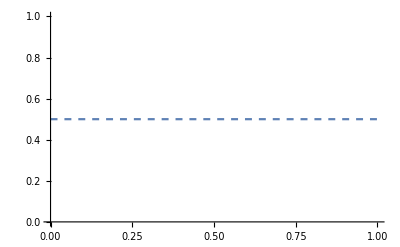

```mathematica
Plot[0.5, {x, 0, Length[ηsatislistnoNR]}, PlotStyle->Dashed]
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

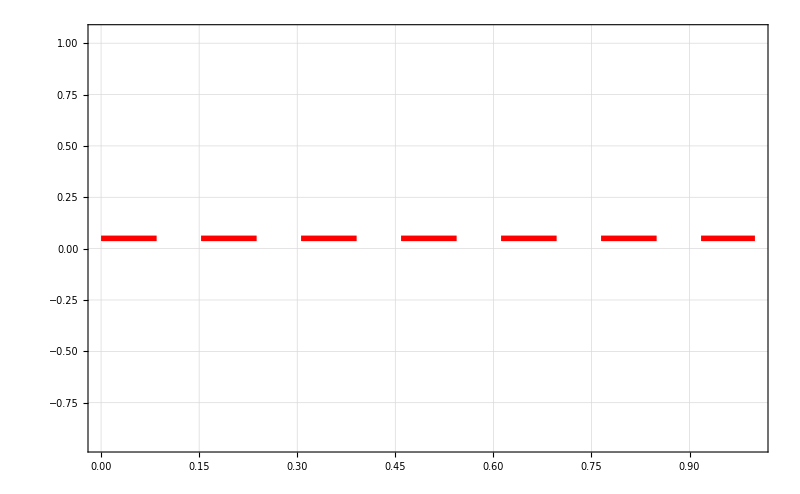

```mathematica
Show[ListPlot[ηsatislistnoNR, PlotStyle->Orange, Joined->True, PlotMarkers->{Automatic, 7}, PlotLegends->Placed[{"Without NR step"},{{Center, 0.95}}]],ListPlot[ηsatislistNR, PlotStyle->Blue, Joined->True, PlotMarkers->{Automatic, 7}, PlotLegends->Placed[{"With NR step"}, {{Center, 0.95}}]], Plot[0.05, {x, 0, Length[ηsatislistnoNR]}, PlotStyle->{Thickness[0.005], Red, Dashing[{0.05, 0.04}]}, PlotLegends->Placed[{"Preset tolerance bound"}, {{Center, 0.95}}]], PlotRange->All, BaseStyle->{FontFamily->"Latin Modern Roman"}, Frame->True,FrameStyle->{Directive[Black,20],Directive[Black,20]}, GridLines->Automatic,PlotStyle->{Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]},PlotMarkers->{"+",20}, FrameLabel->{MaTeX[ToString["\\text{"<>"Discretisation step"<>"}"],Magnification->2],MaTeX[ToString["\\text{Error}~(e_1)"],Magnification->2]},Joined->True, ImageSize->800]
```

```mathematica
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

```mathematica
legvals[[1]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
lsample = Inner[Rule, l, legvals[[1]], List]
```

{l1→1.44582+0. ⅈ,l2→1.56868+0. ⅈ,l3→1.57865+0. ⅈ,l4→1.33939+0. ⅈ,l5→1.15248+0. ⅈ,l6→1.28688+0. ⅈ}

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}];(*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
ηconfig/.qrule/.htanrule//Variables
```

{l1,l2,l3,l4,l5,l6,p1,p2,p3,p4,p5,p6,s1,s2,s3,s4,s5,s6}

```mathematica
Denominator[Together[ηconfig/.qrule/.lsample/.htanrule]]
```

{(1.+p1^2) (1.+p2^2) (1.+s1^2) (1.+s2^2),(1.+p2^2) (1.+p3^2) (1.+s2^2) (1.+s3^2),(1.+p3^2) (1.+p4^2) (1.+s3^2) (1.+s4^2),(1.+p4^2) (1.+p5^2) (1.+s4^2) (1.+s5^2),(1.+p5^2) (1.+p6^2) (1.+s5^2) (1.+s6^2),(1.+p1^2) (1.+p6^2) (1.+s1^2) (1.+s6^2),(1.+p1^2) (1.+p3^2) (1.+s1^2) (1.+s3^2),(1.+p1^2) (1.+p4^2) (1.+s1^2) (1.+s4^2),(1.+p1^2) (1.+p5^2) (1.+s1^2) (1.+s5^2),(1.+p1^2) (1.+p2^2) (1.+p3^2) (1.+p4^2) (1.+s1^2) (1.+s2^2) (1.+s3^2) (1.+s4^2),(1.+p1^2) (1.+p3^2) (1.+p4^2) (1.+p5^2) (1.+s1^2) (1.+s3^2) (1.+s4^2) (1.+s5^2),(1.+p1^2) (1.+p4^2) (1.+p5^2) (1.+p6^2) (1.+s1^2) (1.+s4^2) (1.+s5^2) (1.+s6^2)}

```mathematica
ηlist = Numerator[Together[ηconfig/.qrule/.lsample/.htanrule]];
```

```mathematica
ηlist[[1]]//Simplify
```

-0.141788+1.70079 s1+8.93033 s1^2-1.84531 s2-18.1442 s1 s2-1.84531 s1^2 s2+8.93033 s2^2+1.70079 s1 s2^2-0.141788 s1^2 s2^2+p2 (-3.19617+3.19617 s2^2+s1^2 (-3.19617+3.19617 s2^2))+p2^2 (8.93033-1.84531 s2-0.141788 s2^2+s1 (1.70079-18.1442 s2+1.70079 s2^2)+s1^2 (-0.141788-1.84531 s2+8.93033 s2^2))+p1 (2.94585+2.94585 s2^2+s1^2 (-2.94585-2.94585 s2^2)+p2 (-18.1442+18.1442 s2^2+s1^2 (18.1442-18.1442 s2^2))+p2^2 (2.94585+2.94585 s2^2+s1^2 (-2.94585-2.94585 s2^2)))+p1^2 (8.93033-1.84531 s2-0.141788 s2^2+s1 (1.70079-18.1442 s2+1.70079 s2^2)+s1^2 (-0.141788-1.84531 s2+8.93033 s2^2)+p2^2 (-0.141788-1.84531 s2+8.93033 s2^2+s1^2 (8.93033-1.84531 s2-0.141788 s2^2)+s1 (1.70079-18.1442 s2+1.70079 s2^2))+p2 (-3.19617+3.19617 s2^2+s1^2 (-3.19617+3.19617 s2^2)))

```mathematica
initrule = Inner[Rule, qfull, initpose, List]
```

{x→0.2,y→0,z→1.28,c1→0.2,c2→0,c3→0,ϕ1→0.00305624-8.47269×10^-17 ⅈ,ϕ2→-0.0668855-8.94098×10^-17 ⅈ,ϕ3→0.456963-1.88509×10^-16 ⅈ,ϕ4→0.546956-7.59383×10^-17 ⅈ,ϕ5→-0.0946901-9.49786×10^-17 ⅈ,ϕ6→0.00349011-7.94231×10^-17 ⅈ,ψ1→0.336276-3.59163×10^-18 ⅈ,ψ2→0.286891-1.94522×10^-16 ⅈ,ψ3→-0.0210274-1.35667×10^-16 ⅈ,ψ4→0.0247844-1.74422×10^-16 ⅈ,ψ5→-0.395383-3.49377×10^-17 ⅈ,ψ6→-0.379795-1.31157×10^-16 ⅈ,l1→1.44582+0. ⅈ,l2→1.56868+0. ⅈ,l3→1.57865+0. ⅈ,l4→1.33939+0. ⅈ,l5→1.15248+0. ⅈ,l6→1.28688+0. ⅈ}

```mathematica
ηext/.lsample//Variables
```

{c1,c2,c3,x,y,z,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
(*FK of SRSPM is an unsolved problem*)
```

```mathematica
cJηext@@initpose//SingularValueList
```

{3.08517,2.80986,2.78322,2.52096,2.14729,2.06947,1.56372,1.50228,1.44022,1.382,1.32791,1.22903,1.17389,1.10881,1.0153,0.304377,0.244638,0.157325}

```mathematica
cJηext@@Join[{0.1, 0.1, 0.2, 0,0, 0}, iksol[{0.1, 0.1, 0.2, 0,0, 0}]]//SingularValueList
```

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

SingularValueList[CompiledFunction[…][{0.1,0.1,0.2,0,0,0},iksol[{0.1,0.1,0.2,0,0,0}]]]

```mathematica
bla = {0.1, 0.1, 0.2, 0, 0, 0};
initfrac = Rationalize[Join[bla, iksol[bla]], 0.000001]
```

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]]

```mathematica
fracrule = Inner[Rule, qfull, initfrac, List]
```

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List]

```mathematica
ηlist = Numerator[Together[Rationalize[N[ηext/.fracrule[[-7;;]]/.htanrule], 0.000001]]];
```

Part::take: Cannot take positions -7 through -1 in Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List].

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List]⟦-7;;All⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

Part::take: Cannot take positions -7 through -1 in Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{0.1,0.1,0.2,0.,0.,0.},iksol[{0.1,0.1,0.2,0.,0.,0.}]],List].

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{0.1,0.1,0.2,0.,0.,0.},iksol[{0.1,0.1,0.2,0.,0.,0.}]],List]⟦-7;;All⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

Part::take: Cannot take positions -7 through -1 in Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List].

General::stop: Further output of Part::take will be suppressed during this calculation.

```mathematica
ηlist//Variables
```

{{452/617-(163 (2 c1 c2-2 c3))/(739 (1+c1^2+c2^2+c3^2))-(650 (1+c1^2-c2^2-c3^2))/(1211 (1+c1^2+c2^2+c3^2))+(2 l1 p1 (1-s1^2))/((1+p1^2) (1+s1^2))-x,437/642-(891 (c1 c2+c3))/(830 (1+c1^2+c2^2+c3^2))-(163 (1-c1^2+c2^2-c3^2))/(739 (1+c1^2+c2^2+c3^2))-(2 l1 s1)/(1+s1^2)-y,-(891 (-c2+c1 c3))/(830 (1+c1^2+c2^2+c3^2))-(326 (c1+c2 c3))/(739 (1+c1^2+c2^2+c3^2))+(l1 (1-p1^2) (1-s1^2))/((1+p1^2) (1+s1^2))-z,177/793-(356 (2 c1 c2-2 c3))/(619 (1+c1^2+c2^2+c3^2))+(55 (1+c1^2-c2^2-c3^2))/(711 (1+c1^2+c2^2+c3^2))+(2 l2 p2 (1-s2^2))/((1+p2^2) (1+s2^2))-x,966/991+(110 (c1 c2+c3))/(711 (1+c1^2+c2^2+c3^2))-(356 (1-c1^2+c2^2-c3^2))/(619 (1+c1^2+c2^2+c3^2))-(2 l2 s2)/(1+s2^2)-y,(110 (-c2+c1 c3))/(711 (1+c1^2+c2^2+c3^2))-(712 (c1+c2 c3))/(619 (1+c1^2+c2^2+c3^2))+(l2 (1-p2^2) (1-s2^2))/((1+p2^2) (1+s2^2))-z,-951/995-(401 (2 c1 c2-2 c3))/(1131 (1+c1^2+c2^2+c3^2))+(181 (1+c1^2-c2^2-c3^2))/(394 (1+c1^2+c2^2+c3^2))+(2 l3 p3 (1-s3^2))/((1+p3^2) (1+s3^2))-x,547/1860+(2206 (c1 c2+c3))/(2401 (1+c1^2+c2^2+c3^2))-(401 (1-c1^2+c2^2-c3^2))/(1131 (1+c1^2+c2^2+c3^2))-(2 l3 s3)/(1+s3^2)-y,(2206 (-c2+c1 c3))/(2401 (1+c1^2+c2^2+c3^2))-(841 (c1+c2 c3))/(1186 (1+c1^2+c2^2+c3^2))+(l3 (1-p3^2) (1-s3^2))/((1+p3^2) (1+s3^2))-z,-951/995+(401 (2 c1 c2-2 c3))/(1131 (1+c1^2+c2^2+c3^2))+(181 (1+c1^2-c2^2-c3^2))/(394 (1+c1^2+c2^2+c3^2))+(2 l4 p4 (1-s4^2))/((1+p4^2) (1+s4^2))-x,-547/1860+(2206 (c1 c2+c3))/(2401 (1+c1^2+c2^2+c3^2))+(401 (1-c1^2+c2^2-c3^2))/(1131 (1+c1^2+c2^2+c3^2))-(2 l4 s4)/(1+s4^2)-y,(2206 (-c2+c1 c3))/(2401 (1+c1^2+c2^2+c3^2))+(841 (c1+c2 c3))/(1186 (1+c1^2+c2^2+c3^2))+(l4 (1-p4^2) (1-s4^2))/((1+p4^2) (1+s4^2))-z,177/793+(356 (2 c1 c2-2 c3))/(619 (1+c1^2+c2^2+c3^2))+(55 (1+c1^2-c2^2-c3^2))/(711 (1+c1^2+c2^2+c3^2))+(2 l5 p5 (1-s5^2))/((1+p5^2) (1+s5^2))-x,-966/991+(110 (c1 c2+c3))/(711 (1+c1^2+c2^2+c3^2))+(356 (1-c1^2+c2^2-c3^2))/(619 (1+c1^2+c2^2+c3^2))-(2 l5 s5)/(1+s5^2)-y,(110 (-c2+c1 c3))/(711 (1+c1^2+c2^2+c3^2))+(712 (c1+c2 c3))/(619 (1+c1^2+c2^2+c3^2))+(l5 (1-p5^2) (1-s5^2))/((1+p5^2) (1+s5^2))-z,452/617+(163 (2 c1 c2-2 c3))/(739 (1+c1^2+c2^2+c3^2))-(650 (1+c1^2-c2^2-c3^2))/(1211 (1+c1^2+c2^2+c3^2))+(2 l6 p6 (1-s6^2))/((1+p6^2) (1+s6^2))-x,-437/642-(891 (c1 c2+c3))/(830 (1+c1^2+c2^2+c3^2))+(163 (1-c1^2+c2^2-c3^2))/(739 (1+c1^2+c2^2+c3^2))-(2 l6 s6)/(1+s6^2)-y,-(891 (-c2+c1 c3))/(830 (1+c1^2+c2^2+c3^2))+(326 (c1+c2 c3))/(739 (1+c1^2+c2^2+c3^2))+(l6 (1-p6^2) (1-s6^2))/((1+p6^2) (1+s6^2))-z}/.Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List]⟦-7;;All⟧}

```mathematica
fs = Table[Symbol["f"<>ToString[i]],{i, 18}];
```

```mathematica
Thread[fs == ηlist];
```

## Singularity manifold

```mathematica
g11 = ToExpression[Import["srspm_pos_eq1.txt"]]
```

-0.00106842+0.00254569 x+0.00062447 y-0.00316489 x y+0.00376051 y^2-0.012152 z+0.0207045 x z-0.0167253 y z-0.0049787 x y z+0.0161807 y^2 z-0.00349548 z^2+0.0119489 x z^2-0.119737 y z^2+0.194169 z^3

```mathematica
g11/.Inner[Rule,qfull,initposesC[[4]],List]
```

0.219765-0.183253 ⅈ

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
xpose = {0.2,0,1.28,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp]
```

-Graphics3D-